```mathematica
Quit[];
```

### Intro, always run

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/coscattering/Laura/Xsections

```mathematica
Limp[m1_,m2_,m3_,m4_]:=Module[{E1cmt, E3cmt, E2cmt,p1cmt,p3cmt,p2cmt,tpt,tmt,p1dcmt},
E1cmt=(s+m1^2-m2^2)/(2Sqrt[s]);
p1cmt=Sqrt[E1cmt^2-m1^2];
E2cmt=(s+m2^2-m1^2)/(2Sqrt[s]);
p2cmt=Sqrt[E2cmt^2-m2^2];
E3cmt=(s+m3^2-m4^2)/(2Sqrt[s]);
p3cmt=Sqrt[E3cmt^2-m3^2];
tmt=(m1^2-m2^2-m3^2+m4^2)^2/(4s)-(p1cmt-p3cmt)^2;
tpt=(m1^2-m2^2-m3^2+m4^2)^2/(4s)-(p1cmt+p3cmt)^2;
{tpt,tmt,p1cmt,p2cmt}
]
```

```mathematica
Gammu=10^(-18) (*width of muon in GeV*)
num=.
num0={mph->1000,mX->10,mH->150,mmu->0.105,pref->1,lam->1,mwidth->Gammu*mmu}
num=Join[num0,{s->(mmu+mph)^2*del,del->10.}]
numX=Join[num0,{s->(mmu+mph)^2*del,del->XX}]
```

1/1000000000000000000

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000}

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000,s→del (mmu+mph)^2,del→10.}

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000,s→del (mmu+mph)^2,del→XX}

```mathematica
assum={mx>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&test>0&&nv>0&&x>0&&Ex>0&&Eb>0&&T>0&&Element[{mx,MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,test,nv,x,Ex,Eb,T}, Reals]}
```

{mx>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&test>0&&nv>0&&x>0&&Ex>0&&Eb>0&&T>0&&(mx|MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|test|nv|x|Ex|Eb|T)∈ℝ}

```mathematica
params={MZp->20.,MD1->1.,MD2->1.02,epsilon->1.*^-6,aXM1->127.89999999999999,swsq->0.225,aEWM1->127.89999999999999,MZ->91.188,ttheta->0.00001,ME->0.0005110000000000001,cw->pow[1-swsq,0.5],sw->pow[swsq,0.5],aEW->pow[aEWM1,-1],EE->2 pow[aEW,0.5] pow[π,0.5],aX->pow[aXM1,-1],gX->2 pow[aX,0.5] pow[π,0.5],chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-0.5],SignAux->(MZ-MZp) pow[pow[MZ-MZp,2],-0.5],DZaux->SignAux pow[pow[MZ,4]+pow[MZp,4]-2 pow[MZ,2] pow[MZp,2] (1+2 pow[eta,2] pow[sw,2]),0.5],DZ->0.5 pow[MZ,-2] pow[MZp,-2] (-DZaux pow[MZ,2]+pow[MZ,4]+pow[MZp,4]+pow[MZp,2] (-DZaux-2 pow[eta,2] pow[MZ,2] pow[sw,2])),taAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-0.5 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],0.5]),ca->pow[1+pow[ta,2],-0.5],sa->ta pow[1+pow[ta,2],-0.5],ctheta->pow[1+pow[ttheta,2],-0.5],stheta->ttheta pow[1+pow[ttheta,2],-0.5]}/.pow->Power;
paramsnoMD2=Drop[params,{3}];
```

```mathematica
GeVm2toPb=0.389379 10^9
```

3.89379×10^8

```mathematica
(* to use Izaguare notations*)
reply={alphX->y/eps^2*MZp^4/MD1^4};
(* to use sa in the small epsilon limit*)
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
```

```mathematica
(*not used
replta={chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-1/2],SignAux->(MZ-MZp) pow[pow[MZ-MZp,2],-1/2],DZaux->SignAux pow[pow[MZ,4]+pow[MZp,4]-2 pow[MZ,2] pow[MZp,2] (1+2 pow[eta,2] pow[sw,2]),1/2],DZ->1/2pow[MZ,-2] pow[MZp,-2] (-DZaux pow[MZ,2]+pow[MZ,4]+pow[MZp,4]+pow[MZp,2] (-DZaux-2 pow[eta,2] pow[MZ,2] pow[sw,2])),taAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-1/2 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],1/2]),ca->pow[1+pow[ta,2],-1/2],sa->ta pow[1+pow[ta,2],-1/2]}/.pow->Power;
repltanoDZ={chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-1/2],StaAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-1/2 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],1/2]),ca->pow[1+pow[ta,2],-1/2],sa->ta pow[1+pow[ta,2],-1/2]}/.pow->Power;
*)
```

annihilations

## Getting cross - section chi2 chi2-> ee

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc2c2eeZZp.m"
```

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tp=mylim[[1]]
tm=mylim[[2]]
p1cm=mylim[[3]]
p2cm=mylim[[4]]
p1=.
```

MD2

MD2

0

0

-(√(-MD2^2+s/4)+(√s)/2)^2

-(√(-MD2^2+s/4)-(√s)/2)^2

√(-MD2^2+s/4)

√(-MD2^2+s/4)

```mathematica
vsig0=1/(16*Pi*Sqrt[s^3*p1cm^2]);
Msq=sum/.{pow->Power}//Simplify
```

(ca^2 ctheta^2 EE^2 eta^2 gX^2 stheta^2 (-2 cw^2 sa sw (ca eta+sa sw) (2 MD1^5 MD2 ME^2+MD2^4 ME^2 (-2 ME^2+s+t)+MD1^4 ME^2 (-4 MD2^2-2 ME^2+s+t)+MZp^4 (10 ME^4+s^2+t^2-6 ME^2 (s+t))+2 MD1^3 MD2 (2 MD2^2 ME^2+4 ME^4+MZp^4-2 ME^2 (MZp^2+s+t))-MD2^2 (4 ME^6+MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (-2 MZp^4+2 MZp^2 (s+t)+(s+t)^2))+2 MD1 MD2 (MD2^4 ME^2+4 ME^6-MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (8 MZp^4+2 MZp^2 (s+t)+(s+t)^2)+MD2^2 (4 ME^4+MZp^4-2 ME^2 (MZp^2+s+t)))-MD1^2 (4 MD2^4 ME^2+4 ME^6+MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (-2 MZp^4+2 MZp^2 (s+t)+(s+t)^2)+2 MD2^2 (6 ME^4-MZp^4-ME^2 (4 MZp^2+3 (s+t)))))+cw^4 sa^2 (-2 MD1^5 MD2 ME^2+MD2^4 ME^2 (2 ME^2-s-t)+MD1^4 ME^2 (4 MD2^2+2 ME^2-s-t)+MZp^4 (2 ME^4+s^2+t^2-2 ME^2 (s+t))+2 MD1^3 MD2 (-2 MD2^2 ME^2-4 ME^4+MZp^4+2 ME^2 (MZp^2+s+t))+MD2^2 (4 ME^6-MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (2 MZp^4+2 MZp^2 (s+t)+(s+t)^2))-2 MD1 MD2 (MD2^4 ME^2+4 ME^6+MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (s+t) (2 MZp^2+s+t)+MD2^2 (4 ME^4-MZp^4-2 ME^2 (MZp^2+s+t)))+MD1^2 (4 MD2^4 ME^2+4 ME^6-MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (2 MZp^4+2 MZp^2 (s+t)+(s+t)^2)+2 MD2^2 (6 ME^4+MZp^4-ME^2 (4 MZp^2+3 (s+t)))))-sw^2 (ca eta+sa sw)^2 (2 MD1^5 MD2 ME^2+MD2^4 ME^2 (-2 ME^2+s+t)+MD1^4 ME^2 (-4 MD2^2-2 ME^2+s+t)+2 MD1^3 MD2 (2 MD2^2 ME^2+4 ME^4-5 MZp^4-2 ME^2 (MZp^2+s+t))+MZp^4 (-26 ME^4+18 ME^2 (s+t)-5 (s^2+t^2))-MD2^2 (4 ME^6-5 MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (10 MZp^4+2 MZp^2 (s+t)+(s+t)^2))+2 MD1 MD2 (MD2^4 ME^2+4 ME^6+5 MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (-16 MZp^4+2 MZp^2 (s+t)+(s+t)^2)+MD2^2 (4 ME^4-5 MZp^4-2 ME^2 (MZp^2+s+t)))-MD1^2 (4 MD2^4 ME^2+4 ME^6-5 MZp^4 (s+t)-4 ME^4 (MZp^2+s+t)+ME^2 (10 MZp^4+2 MZp^2 (s+t)+(s+t)^2)+2 MD2^2 (6 ME^4+5 MZp^4-ME^2 (4 MZp^2+3 (s+t)))))))/(4 chi^2 cw^2 MZp^4 sw^2 (-MD1^2-MD2^2-2 ME^2+MZp^2+s+t)^2)

```mathematica
vsig0
```

1/(16 π √(s^3 (-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))))

```mathematica
(*relative velo in NR limit*)
sol=Solve[4p1cm/Sqrt[s]==vrel,s];
ss=Series[s/.sol[[1,1]],{vrel,0,2}]
s1=SeriesCoefficient[ss,0]+SeriesCoefficient[ss,2]vrel^2
```

4 MD2^2+MD2^2 vrel^2+O[vrel]^3

4 MD2^2+MD2^2 vrel^2

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp;
IntMm=IntM/.t->tm;
```

```mathematica
sv=vsig0*(IntMm-IntMp)//.{s->s1};
```

```mathematica
ieps=2
replann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2]};
svs=Simplify[Series[sv/.replann,{vrel,0,1},{sa,0,1},{eps,0,ieps}], assum]
SeriesCoefficient[%,{0,0,ieps}]*eps^ieps
```

2

(((10 alph alphX ctheta^4 MD2^2 π eps^2)/(cw^4 (-4 MD2^2+MZp^2)^2)+O[eps]^3)+((4 alph alphX ctheta^4 MD2^2 (MZ^2-MZp^2) π (cw^2-5 sw^2) eps)/(cw^3 (4 MD2^2-MZ^2) (-4 MD2^2+MZp^2)^2 sw)+O[eps]^3) sa+O[sa]^2)+O[vrel]^2

(10 alph alphX ctheta^4 eps^2 MD2^2 π)/(cw^4 (-4 MD2^2+MZp^2)^2)

## Getting cross - section chi1 chi1-> ee

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1c1eeZZp.m"
```

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tp=mylim[[1]]
tm=mylim[[2]]
p1cm=mylim[[3]]
p2cm=mylim[[4]]
p1=.
```

MD1

MD1

0

0

-(√(-MD1^2+s/4)+(√s)/2)^2

-(√(-MD1^2+s/4)-(√s)/2)^2

√(-MD1^2+s/4)

√(-MD1^2+s/4)

```mathematica
vsig0=1/(16*Pi*Sqrt[s^3*p1cm^2]);
Msq=sum/.{pow->Power}//Simplify
```

1/(4 chi^2 cw^2 (MZ^2-s)^2 (MZp^2-s)^2 sw^2)EE^2 eta^2 gX^2 stheta^4 (5 ca^4 eta^2 (MZ^2-s)^2 sw^2+5 eta^2 (MZp^2-s)^2 sa^4 sw^2-2 ca^3 eta (MZ^2-MZp^2) (MZ^2-s) sa sw (cw^2-5 sw^2)-2 ca eta (MZ^2-MZp^2) (MZp^2-s) sa^3 sw (cw^2-5 sw^2)+ca^2 sa^2 (cw^4 (MZ^2-MZp^2)^2-2 cw^2 (MZ^2-MZp^2)^2 sw^2+5 sw^2 (2 eta^2 (MZ^2-s) (MZp^2-s)+(MZ^2-MZp^2)^2 sw^2))) (2 MD1^4+s^2-4 MD1^2 t+2 s t+2 t^2)

```mathematica
(*relative velo in NR limit*)
sol=Solve[4p1cm/Sqrt[s]==vrel,s];
ss=Series[s/.sol[[1,1]],{vrel,0,2}]
s1=SeriesCoefficient[ss,0]+SeriesCoefficient[ss,2]vrel^2
```

4 MD1^2+MD1^2 vrel^2+O[vrel]^3

4 MD1^2+MD1^2 vrel^2

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp;
IntMm=IntM/.t->tm;
```

```mathematica
sv=vsig0*(IntMm-IntMp)//.{s->s1};
```

```mathematica
iMD1=2
ieps=2
replann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2]};
svs=Simplify[Series[sv/.replann,{vrel,0,1},{sa,0,1},{eps,0,ieps},{MD1,0,iMD1}], assum]
SeriesCoefficient[%,{0,0,ieps,iMD1}]*MD1^iMD1*eps^ieps
```

2

2

((((10 alph alphX π stheta^4 MD1^2)/(cw^4 MZp^4)+O[MD1]^3) eps^2+O[eps]^3)+((-(4 (alph alphX (MZ^2-MZp^2) π stheta^4 (cw^2-5 sw^2)) MD1^2)/(cw^3 MZ^2 MZp^4 sw)+O[MD1]^3) eps+O[eps]^3) sa+O[sa]^2)+O[vrel]^2

(10 alph alphX eps^2 MD1^2 π stheta^4)/(cw^4 MZp^4)

co-annihilations

## Getting cross - section chi1 chi2-> ee

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1c2eeZZp.m"
```

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tp=mylim[[1]]
tm=mylim[[2]]
p1cm=mylim[[3]]
p2cm=mylim[[4]]
p1=.
```

MD1

MD2

0

0

((MD1^2-MD2^2)^2)/(4 s)-((√s)/2+√(-MD1^2+((MD1^2-MD2^2+s)^2)/(4 s)))^2

((MD1^2-MD2^2)^2)/(4 s)-(-(√s)/2+√(-MD1^2+((MD1^2-MD2^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-MD2^2+s)^2)/(4 s))

√(-MD2^2+((-MD1^2+MD2^2+s)^2)/(4 s))

```mathematica
vsig0=1/(16*Pi*Sqrt[s^3*p1cm^2]);
Msq=sum/.{pow->Power}//Simplify
```

1/(4 chi^2 cw^2 (MZ^2-s)^2 (MZp^2-s)^2 sw^2)ctheta^2 EE^2 eta^2 gX^2 stheta^2 (5 ca^4 eta^2 (MZ^2-s)^2 sw^2+5 eta^2 (MZp^2-s)^2 sa^4 sw^2-2 ca^3 eta (MZ^2-MZp^2) (MZ^2-s) sa sw (cw^2-5 sw^2)-2 ca eta (MZ^2-MZp^2) (MZp^2-s) sa^3 sw (cw^2-5 sw^2)+ca^2 sa^2 (cw^4 (MZ^2-MZp^2)^2-2 cw^2 (MZ^2-MZp^2)^2 sw^2+5 sw^2 (2 eta^2 (MZ^2-s) (MZp^2-s)+(MZ^2-MZp^2)^2 sw^2))) (2 MD1 MD2 s+s^2+MD1^2 (2 MD2^2-s-2 t)+2 s t+2 t^2-MD2^2 (s+2 t))

```mathematica
(*relative velo in NR limit*)
sol=Solve[4p1cm/Sqrt[s]==vrel,s];
ss=Simplify[Series[s/.sol[[1,1]],{vrel,0,2}],assum];
s1=SeriesCoefficient[ss,0]+SeriesCoefficient[ss,2]vrel^2
Series[%/.MD2->MD1+del,{del,0,1}]
```

(MD1+MD2)^2+((MD1+MD2)^4 vrel^2)/(16 MD1 MD2)

(4 MD1^2+MD1^2 vrel^2)+(4 MD1+MD1 vrel^2) del+O[del]^2

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp;
IntMm=IntM/.t->tm;
```

```mathematica
sv=vsig0*(IntMm-IntMp)//.{s->s1};
```

```mathematica
ieps=2
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2]};
svs=Simplify[Series[sv/.replcoann,{vrel,0,1},{sa,0,1},{eps,0,ieps}], assum]
SeriesCoefficient[%,{0,0,ieps}]*eps^ieps
```

2

(((10 alph alphX ctheta^2 MD1 MD2 π stheta^2 eps^2)/(cw^4 (MD1^2+2 MD1 MD2+MD2^2-MZp^2)^2)+O[eps]^3)+((4 alph alphX ctheta^2 MD1 MD2 (MZ^2-MZp^2) π stheta^2 (cw^2-5 sw^2) eps)/(cw^3 (MD1^2+2 MD1 MD2+MD2^2-MZ^2) (MD1^2+2 MD1 MD2+MD2^2-MZp^2)^2 sw)+O[eps]^3) sa+O[sa]^2)+O[vrel]^2

(10 alph alphX ctheta^2 eps^2 MD1 MD2 π stheta^2)/(cw^4 (MD1^2+2 MD1 MD2+MD2^2-MZp^2)^2)

scatterings

## Getting cross - section chi1 e-> chi1 e

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec1e.m"
```

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tp=mylim[[1]]
tm=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

0

0

MD1

MD1^4/s-(1/2 √(((-MD1^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2

MD1^4/s-(-1/2 √(((-MD1^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2

1/2 √(((MD1^2-s)^2)/s)

```mathematica
(*here we compute sigma not sigma x v*)
sig0=1/(64Pi s)/p1cm^2;
Msq=sum/.{pow->Power}//Simplify
```

(EE^2 eta^2 gX^2 stheta^4 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)) (ca^2 sa^2 (cw^4 (MZ^2-MZp^2)^2-2 cw^2 (MZ^2-MZp^2)^2 sw^2+5 (MZ^2-MZp^2)^2 sw^4+10 eta^2 sw^2 (2 MD1^2-MZ^2-s-t) (2 MD1^2-MZp^2-s-t))+2 ca^3 eta (MZ^2-MZp^2) sa sw (-cw^2+5 sw^2) (-2 MD1^2+MZ^2+s+t)+5 ca^4 eta^2 sw^2 (-2 MD1^2+MZ^2+s+t)^2+2 ca eta (MZ^2-MZp^2) sa^3 sw (-cw^2+5 sw^2) (-2 MD1^2+MZp^2+s+t)+5 eta^2 sa^4 sw^2 (-2 MD1^2+MZp^2+s+t)^2))/(4 chi^2 cw^2 sw^2 (-2 MD1^2+MZ^2+s+t)^2 (-2 MD1^2+MZp^2+s+t)^2)

```mathematica
(*relative velo in NR limit*)
sol=Solve[4p1cm/Sqrt[s]==vrel,s]
ss=Simplify[Series[s/.sol[[1,1]],{vrel,0,2}],assum];
s1=SeriesCoefficient[ss,0]+SeriesCoefficient[ss,1]vrel
```

{{s→-(2 MD1^2)/(-2+vrel)},{s→(2 MD1^2)/(2+vrel)}}

MD1^2+(MD1^2 vrel)/2

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp;
IntMm=IntM/.t->tm;
```

```mathematica
svt=sig0*(IntMm-IntMp);
sv=svt//.{s->s1};
```

```mathematica
ieps=2;
ivrel=2;
iMD1=2;
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
svs=Simplify[Series[sv//.replcoann,{eps,0,ieps},{MD1,0,iMD1},{vrel,0,4}]/.sw->Sqrt[1-cw^2], assum]
svlim=SeriesCoefficient[%,{ivrel,ieps,iMD1}]*vrel^ivrel*eps^ieps*MD1^iMD1/.reply/.MZp->0
```

(((alph alphX (5 MZp^4+12 cw^2 MZp^2 (MZ^2-MZp^2)+8 cw^4 (MZ^2-MZp^2)^2) π stheta^4 vrel^2)/(16 cw^4 MZ^4 MZp^4)-((alph alphX (5 MZp^4+12 cw^2 MZp^2 (MZ^2-MZp^2)+8 cw^4 (MZ^2-MZp^2)^2) π stheta^4) vrel^3)/(32 (cw^4 MZ^4 MZp^4))+(alph alphX (5 MZp^4+12 cw^2 MZp^2 (MZ^2-MZp^2)+8 cw^4 (MZ^2-MZp^2)^2) π stheta^4 vrel^4)/(48 cw^4 MZ^4 MZp^4)+O[vrel]^5) MD1^2+O[MD1]^3) eps^2+O[eps]^3

(alph π stheta^4 vrel^2 y)/(2 MD1^2)

```mathematica
(* Here I check that the result above in the small velocity limit gives exactly the same result as the full expression, notice that these numerical results agree with calchep output!!*)
ptest=MD1/30/.params;
ss=Solve[p1cm==ptest,s]/.params
svt*GeVm2toPb/.ss[[2,1]]//.params
svlim*GeVm2toPb//.{alph->1/aEWM1,del->Sqrt[MD2^2-MD1^2],y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
```

{{s→0.935519},{s→1.06893}}

4.11283×10^-35

4.1544×10^-35

```mathematica
svlim*ctheta^2/stheta^2
%//.{alph->1/aEWM1,del->Sqrt[MD2^2-MD1^2],y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
```

(alph ctheta^2 π stheta^2 vrel^2 y)/(2 MD1^2)

1.06693×10^-33

## Getting cross - section chi1 e-> chi1 e Zp

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec1e-Zp.m"
```

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tp=mylim[[1]]
tm=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

ME

ME

MD1

((2 MD1^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD1^2+ME^2+s)^2)/(4 s)))^2

((2 MD1^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD1^2+ME^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))

```mathematica
(*here we compute sigma not sigma x v*)
sig0=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power,ME->0}//Simplify
```

(ca^2 EE^2 eta^2 gX^2 stheta^4 (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2) (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/(4 chi^2 cw^2 sw^2 (-2 MD1^2+MZp^2+s+t)^2)

```mathematica
Msq//.{ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
Series[%,{eps,0,2}]/.sw->Sqrt[1-cw^2];
Msqlimc1c1=SeriesCoefficient[%,2]*eps^2
```

(2 EE^2 eps^2 gX^2 stheta^4 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)

```mathematica
(2 EE^2 eps^2 gX^2 stheta^4 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)
```

(2 EE^2 eps^2 gX^2 stheta^4 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)

```mathematica
(*relative velo in NR limit*)
sol=Solve[4p1cm/Sqrt[s]==vrel/.ME->0,s]
ss=Simplify[Series[s/.sol[[1,1]],{vrel,0,2}],assum];
s1=SeriesCoefficient[ss,0]+SeriesCoefficient[ss,1]vrel
```

{{s→-(2 MD1^2)/(-2+vrel)},{s→(2 MD1^2)/(2+vrel)}}

MD1^2+(MD1^2 vrel)/2

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
svt=sig0*(IntMm-IntMp);
sv=svt//.{s->s1};
```

```mathematica
IntM=Integrate[Msqlimc1c1,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
svlim=sig0*(IntMm-IntMp)//Simplify;
svlimc1c1=%;
```

```mathematica
ieps=2;
ivrel=2;
iMD1=2;
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
svs=Simplify[Series[sv//.replcoann,{eps,0,ieps},{MD1,0,iMD1},{vrel,0,4}]/.sw->Sqrt[1-cw^2], assum];
svlim2=SeriesCoefficient[%,{ivrel,ieps,iMD1}]*vrel^ivrel*eps^ieps*MD1^iMD1/.reply/.MZp->0
```

(alph π stheta^4 vrel^2 y)/(2 MD1^2)

```mathematica
(* Here I check that the result above in the small velocity limit gives exactly the same result as the full expression, notice that these numerical results agree with calchep output!!*)
ptest=MD1/30/.params;
ss=Solve[p1cm==ptest,s]/.params
svt*GeVm2toPb/.ss[[2,1]]//.params
svlim2*GeVm2toPb//.{alph->1/aEWM1,del->Sqrt[MD2^2-MD1^2],y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
```

{{s→0.935511},{s→1.06893}}

4.14456×10^-35

4.1544×10^-35

```mathematica
svlim2*ctheta^2/stheta^2
%//.{alph->1/aEWM1,del->Sqrt[MD2^2-MD1^2],y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
```

(alph ctheta^2 π stheta^2 vrel^2 y)/(2 MD1^2)

1.06693×10^-33

## Getting cross - section chi1 e-> chi2 e my version using large s

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

0

0

MD2

((MD1^2+MD2^2)^2)/(4 s)-(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2)^2)/(4 s)-(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2

1/2 √(((MD1^2-s)^2)/s)

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.{ME->0,MD1->0,MD2->0};
Msq=sum/.{pow->Power,ME->0,MD1->0,MD2->0}//Simplify
MyMSq=%;
```

1/(4 chi^2 cw^2 sw^2 (MZ^2+s+t)^2 (MZp^2+s+t)^2)ctheta^2 EE^2 eta^2 gX^2 stheta^2 (s^2+t^2) (-2 ca^3 eta (MZ^2-MZp^2) sa sw (cw^2-5 sw^2) (MZ^2+s+t)+5 ca^4 eta^2 sw^2 (MZ^2+s+t)^2-2 ca eta (MZ^2-MZp^2) sa^3 sw (cw^2-5 sw^2) (MZp^2+s+t)+5 eta^2 sa^4 sw^2 (MZp^2+s+t)^2+ca^2 sa^2 (cw^4 (MZ^2-MZp^2)^2-2 cw^2 (MZ^2-MZp^2)^2 sw^2+5 (MZ^2-MZp^2)^2 sw^4+10 eta^2 sw^2 (MZ^2+s+t) (MZp^2+s+t)))

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.{ME->0,MD1->0,MD2->0};
IntMm=IntM/.t->tm/.{ME->0,MD1->0,MD2->0};
```

```mathematica
sv=sig0*(IntMp-IntMm)
```

1/(16 π s^2)(-1/(4 chi^2 cw^2 sw^2)ctheta^2 EE^2 eta^2 gX^2 stheta^2 (-5 eta^2 s (ca^2+sa^2)^2 sw^2-(ca^2 (MZp^4+2 MZp^2 s+2 s^2) (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2))/MZp^2-((MZ^4+2 MZ^2 s+2 s^2) sa^2 (5 eta^2 sa^2 sw^2+2 ca eta sa sw (cw^2-5 sw^2)+ca^2 (cw^4-2 cw^2 sw^2+5 sw^4)))/MZ^2-1/(MZ^2-MZp^2)2 sa (5 eta^2 (MZ^2-MZp^2) (MZ^2+s) sa^3 sw^2+ca^3 eta (MZ^4+2 MZ^2 s+2 s^2) sw (cw^2-5 sw^2)+ca eta (MZ^4-2 MZ^2 MZp^2-2 s (MZp^2+s)) sa^2 sw (cw^2-5 sw^2)-ca^2 sa (cw^4 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))-5 eta^2 (MZ^4+2 MZ^2 s+2 s^2) sw^2-2 cw^2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^2+5 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^4)) Log[MZ^2]-1/(MZ^2-MZp^2)2 ca (5 ca^3 eta^2 (MZ^2-MZp^2) (MZp^2+s) sw^2-ca^2 eta (-MZp^4+2 s^2+2 MZ^2 (MZp^2+s)) sa sw (cw^2-5 sw^2)+eta (MZp^4+2 MZp^2 s+2 s^2) sa^3 sw (cw^2-5 sw^2)+ca sa^2 (cw^4 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))-5 eta^2 (MZp^4+2 MZp^2 s+2 s^2) sw^2-2 cw^2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^2+5 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^4)) Log[MZp^2])+1/(4 chi^2 cw^2 sw^2)ctheta^2 EE^2 eta^2 gX^2 stheta^2 (-(ca^2 (MZp^4+2 MZp^2 s+2 s^2) (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2))/(MZp^2+s)-((MZ^4+2 MZ^2 s+2 s^2) sa^2 (5 eta^2 sa^2 sw^2+2 ca eta sa sw (cw^2-5 sw^2)+ca^2 (cw^4-2 cw^2 sw^2+5 sw^4)))/(MZ^2+s)-1/(MZ^2-MZp^2)2 sa (5 eta^2 (MZ^2-MZp^2) (MZ^2+s) sa^3 sw^2+ca^3 eta (MZ^4+2 MZ^2 s+2 s^2) sw (cw^2-5 sw^2)+ca eta (MZ^4-2 MZ^2 MZp^2-2 s (MZp^2+s)) sa^2 sw (cw^2-5 sw^2)-ca^2 sa (cw^4 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))-5 eta^2 (MZ^4+2 MZ^2 s+2 s^2) sw^2-2 cw^2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^2+5 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^4)) Log[MZ^2+s]-1/(MZ^2-MZp^2)2 ca (5 ca^3 eta^2 (MZ^2-MZp^2) (MZp^2+s) sw^2-ca^2 eta (-MZp^4+2 s^2+2 MZ^2 (MZp^2+s)) sa sw (cw^2-5 sw^2)+eta (MZp^4+2 MZp^2 s+2 s^2) sa^3 sw (cw^2-5 sw^2)+ca sa^2 (cw^4 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))-5 eta^2 (MZp^4+2 MZp^2 s+2 s^2) sw^2-2 cw^2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^2+5 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^4)) Log[MZp^2+s]))

```mathematica
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->epsilon Power[cw,-1],eta->chi Power[1-Power[chi,2],-1/2],MD2->Sqrt[MD1^2+del^2],sa->-sw epsilon/cw};
svs=Simplify[Series[sv//.replcoann,{epsilon,0,ieps},{MZp,0,1},{MZ,0,1}], assum]/.sw->Sqrt[1-cw^2]
```

((4 alph alphX ctheta^2 π stheta^2)/MZp^2+(-(alph alphX ctheta^2 π stheta^2 (-5+12 cw^2-8 cw^4-24 cw^2 Log[MZ]+32 cw^4 Log[MZ]+24 cw^2 Log[MZp]-32 cw^4 Log[MZp]))/(2 cw^4 MZ^2)-(alph alphX ctheta^2 π stheta^2 (-5+24 cw^2-32 cw^4-20 Log[MZ]+32 cw^4 Log[MZ]-32 cw^4 Log[MZp]+10 Log[s]))/(4 (cw^4 s))+O[MZ]^2)+O[MZp]^2) epsilon^2+O[epsilon]^3

## Getting cross - section chi1 e-> chi2 e (Zp only) (test=(m2-m1)/m1, vrel=2(2test+test^2)+test2) BEST OPTION

### getting M^2

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e-vSam-Zp.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

ME

ME

MD2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power}/.ME->0//Simplify
```

(ca^2 ctheta^2 EE^2 eta^2 gX^2 stheta^2 (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2) (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/(4 chi^2 cw^2 sw^2 (-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* Amplitude squared in eps->0 limit, propto eps^2*)
Msq//.{ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
Series[%,{eps,0,2}]/.sw->Sqrt[1-cw^2];
Msqlim=SeriesCoefficient[%,2]*eps^2
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/(-MD1^2-MD2^2+MZp^2+s+t)^2

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
Msqlimc1c2=Msqlim/.MD2->MD1//Simplify
Msqlimc1c1
Msqlimc1c2/Msqlimc1c1
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)

Msqlimc1c1

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/(Msqlimc1c1 (-2 MD1^2+MZp^2+s+t)^2)

### getting xsections and testing limit MD2->MD1 analytics ok

```mathematica
tp
```

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

```mathematica
tm
```

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

```mathematica
(* cross-section*)
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
sv=sig0*(IntMp-IntMm);
```

```mathematica
(* cross-section eps->0 limit, propto eps^2*)
IntM=Integrate[Msqlim,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
svlim=sig0*(IntMp-IntMm);
```

```mathematica
sig0
```

1/(64 π s (-MD1^2+((MD1^2+s)^2)/(4 s)))

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
svlimc1c2=svlim/.MD2->MD1//Simplify
svlimc1c1
Rsv=svlimc1c2/svlimc1c1
```

1/(8 π (MD1^2-s)^2)ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s])

svlimc1c1

1/(8 π (MD1^2-s)^2 svlimc1c1)ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s])

```mathematica
(*Weird, when I first give all params except M2 and then M2 it gives a different numerical result...*)
ptest=MD1/30/.params;
ss=Solve[p1cm==ptest,s]/.params
tpt=tp/.ss[[2,1]]//.params;
tmt=tm/.ss[[2,1]]//.params;
If[tpt>tmt,sv/.ss[[2,1]]//.params,-sv/.ss[[2,1]]//.params]*GeVm2toPb
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.paramsnoMD2/.params
(*test0*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
test*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.vrel->4*ptest/MD1//.params*)
```

{{s→0.935511},{s→1.06893}}

6.75237×10^-26

6.8679×10^-26

6.54179×10^-26

6.8679×10^-26

```mathematica
myvrel=4*ptest/MD1//.params
mys=MD1^2(1+myvrel/2)//.params
```

0.133333

1.06667

```mathematica
svlimc1c1*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
svlimc1c1*Rsv*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
```

3.89379×10^8 svlimc1c1

4.15061×10^-25

### getting series of xsection in test=(MD2-MD1)/MD1=test and vrel =2 (2+test) test+test2

```mathematica
Series[svlim//.{MD2->MD1(1+test),s->MD1^2(1+vrel/2),vrel->(4+2test)test+test2},{test,0,1},{test2,0,2}]//Normal;
svseries=Simplify[%,assum]
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1,test->del/MD1,test2->vrel-(4+2test)test}//.params
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (-1+2 test) test2^2)/(32 MZp^4 π)

6.19117×10^-26

```mathematica
svseries//.replcoann//.reply
```

-(alph ctheta^2 π stheta^2 (-1+2 test) test2^2 y)/(2 MD1^2)

#### Nastya’s edition

```mathematica
svlim
```

1/(64 π s (-MD1^2+((MD1^2+s)^2)/(4 s)))(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2+MD2^2)^2)/(4 s)-(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2+(2 MD1 MD2 MZp^2+MZp^4+MD1^2 (2 MD2^2-MZp^2-2 s)+2 MZp^2 s+2 s^2-MD2^2 (MZp^2+2 s))/(MD1^2+MD2^2-MZp^2-((MD1^2+MD2^2)^2)/(4 s)-s+(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2)+(MD1^2-2 MD1 MD2+MD2^2-2 (MZp^2+s)) Log[-MD1^2-MD2^2+MZp^2+((MD1^2+MD2^2)^2)/(4 s)+s-(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2])-2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2+MD2^2)^2)/(4 s)-(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2+(2 MD1 MD2 MZp^2+MZp^4+MD1^2 (2 MD2^2-MZp^2-2 s)+2 MZp^2 s+2 s^2-MD2^2 (MZp^2+2 s))/(MD1^2+MD2^2-MZp^2-((MD1^2+MD2^2)^2)/(4 s)-s+(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2)+(MD1^2-2 MD1 MD2+MD2^2-2 (MZp^2+s)) Log[-MD1^2-MD2^2+MZp^2+((MD1^2+MD2^2)^2)/(4 s)+s-(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2]))

tests

## Getting cross - section chi1 e-> chi2 e my version using vrel small-> good approximation!

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

0

0

MD2

((MD1^2+MD2^2)^2)/(4 s)-(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2)^2)/(4 s)-(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2

1/2 √(((MD1^2-s)^2)/s)

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power,ME->0}//Simplify
MyMSq=%;
```

(ctheta^2 EE^2 eta^2 gX^2 stheta^2 (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)) (ca^2 sa^2 (cw^4 (MZ^2-MZp^2)^2-2 cw^2 (MZ^2-MZp^2)^2 sw^2+5 (MZ^2-MZp^2)^2 sw^4+10 eta^2 sw^2 (MD1^2+MD2^2-MZ^2-s-t) (MD1^2+MD2^2-MZp^2-s-t))+2 ca^3 eta (MZ^2-MZp^2) sa sw (-cw^2+5 sw^2) (-MD1^2-MD2^2+MZ^2+s+t)+5 ca^4 eta^2 sw^2 (-MD1^2-MD2^2+MZ^2+s+t)^2+2 ca eta (MZ^2-MZp^2) sa^3 sw (-cw^2+5 sw^2) (-MD1^2-MD2^2+MZp^2+s+t)+5 eta^2 sa^4 sw^2 (-MD1^2-MD2^2+MZp^2+s+t)^2))/(4 chi^2 cw^2 sw^2 (-MD1^2-MD2^2+MZ^2+s+t)^2 (-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(*relative velo in NR limit*)
sol=Solve[4p1cm/Sqrt[s]==vrel,s]/.ME->0
ptest=MD1/30/.params;
sol/.vrel->4*ptest/MD1/.params
ss=Simplify[Series[s/.sol[[1,1]],{vrel,0,2}],assum]
s1=SeriesCoefficient[ss,0]+SeriesCoefficient[ss,1]vrel
s1/.vrel->4*ptest/MD1/.params
(* the CM energy can be computed with leading order terms in vrel*)
```

{{s→-(2 MD1^2)/(-2+vrel)},{s→(2 MD1^2)/(2+vrel)}}

{{s→1.07143},{s→0.9375}}

MD1^2+(MD1^2 vrel)/2+(MD1^2 vrel^2)/4+O[vrel]^3

MD1^2+(MD1^2 vrel)/2

1.06667

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
```

```mathematica
sv=sig0*(IntMp-IntMm)//.{s->s1};
```

```mathematica
IntMp/.MD1-> 0
```

1/(4 chi^2 cw^2 sw^2)ctheta^2 EE^2 eta^2 gX^2 stheta^2 (5 eta^2 (MD2^4/(4 s)-((√s)/2-1/2 √(((-MD2^2+s)^2)/s))^2) (ca^2+sa^2)^2 sw^2+(ca^2 (MZp^4+2 MZp^2 s+2 s^2-MD2^2 (MZp^2+2 s)) (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2))/(MD2^2-MZp^2-MD2^4/(4 s)-s+((√s)/2-1/2 √(((-MD2^2+s)^2)/s))^2)+((MZ^4+2 MZ^2 s+2 s^2-MD2^2 (MZ^2+2 s)) sa^2 (5 eta^2 sa^2 sw^2+2 ca eta sa sw (cw^2-5 sw^2)+ca^2 (cw^4-2 cw^2 sw^2+5 sw^4)))/(MD2^2-MZ^2-MD2^4/(4 s)-s+((√s)/2-1/2 √(((-MD2^2+s)^2)/s))^2)-1/(MZ^2-MZp^2)sa (-5 eta^2 (MZ^2-MZp^2) (MD2^2-2 (MZ^2+s)) sa^3 sw^2+2 ca^3 eta (MZ^4+2 MZ^2 s+2 s^2-MD2^2 (MZ^2+2 s)) sw (cw^2-5 sw^2)+2 ca eta (MZ^4+MD2^2 MZp^2-2 MZ^2 MZp^2+2 MD2^2 s-2 MZp^2 s-2 s^2) sa^2 sw (cw^2-5 sw^2)+ca^2 sa (cw^4 (MD2^2 (MZ^2+MZp^2+4 s)-2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)))+2 cw^2 (2 MZ^2 (MZp^2+s)+2 s (MZp^2+2 s)-MD2^2 (MZ^2+MZp^2+4 s)) sw^2+5 sw^2 (2 eta^2 (MZ^4+2 MZ^2 s+2 s^2-MD2^2 (MZ^2+2 s))+(MD2^2 (MZ^2+MZp^2+4 s)-2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))) sw^2))) Log[-MD2^2+MZ^2+MD2^4/(4 s)+s-((√s)/2-1/2 √(((-MD2^2+s)^2)/s))^2]+1/(MZ^2-MZp^2)ca (5 ca^3 eta^2 (MZ^2-MZp^2) (MD2^2-2 (MZp^2+s)) sw^2+2 ca^2 eta (2 MZ^2 MZp^2-MZp^4+2 MZ^2 s+2 s^2-MD2^2 (MZ^2+2 s)) sa sw (cw^2-5 sw^2)-2 eta (MZp^4+2 MZp^2 s+2 s^2-MD2^2 (MZp^2+2 s)) sa^3 sw (cw^2-5 sw^2)+ca sa^2 (cw^4 (MD2^2 (MZ^2+MZp^2+4 s)-2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)))+2 cw^2 (2 MZ^2 (MZp^2+s)+2 s (MZp^2+2 s)-MD2^2 (MZ^2+MZp^2+4 s)) sw^2+5 sw^2 (2 eta^2 (MZp^4+2 MZp^2 s+2 s^2-MD2^2 (MZp^2+2 s))+(MD2^2 (MZ^2+MZp^2+4 s)-2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))) sw^2))) Log[-MD2^2+MZp^2+MD2^4/(4 s)+s-((√s)/2-1/2 √(((-MD2^2+s)^2)/s))^2])

```mathematica
sv*GeVm2toPb/.vrel->4*ptest/MD1//.paramsnoMD2/.MD2->MD2/.params
sv*GeVm2toPb/.vrel->4*ptest/MD1//.params
```

6.294×10^-26

5.245×10^-26

```mathematica
(*checking that I agree with the definition of ta*)
ta//.params
myt2a=2 sw eta/(1-(sw eta)^2-DZ);
Series[myt2a,{eta,0,1},{DZ,0,1}]
Tan[ArcTan[myt2a]/2]//.params
(*I agree up to the overall sign*)
```

-5.65945×10^-7

(2 sw+2 sw DZ+O[DZ]^2) eta+O[eta]^2

5.66045×10^-7

```mathematica
sa//.params
mysa=- sw epsilon/cw//.params (*My epsilon is their epsilon/cw*)
```

-5.65945×10^-7

-5.38816×10^-7

```mathematica
(*Here I take into account that sin alpha is epsilon dependent*)
ieps=2;
ivrel=1;
isa=1;
idel=4;
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->epsilon Power[cw,-1],eta->chi Power[1-Power[chi,2],-1/2],MD2->Sqrt[MD1^2+del^2],sa->-sw epsilon/cw};
svs=Simplify[Series[sv//.replcoann,{epsilon,0,ieps},{vrel,0,ivrel},{del,0,idel}], assum]
```

$Aborted

```mathematica
del=.
is={2,0,4};
SeriesCoefficient[svs,is]*eps^is[[1]]*vrel^is[[2]]*del^is[[3]]/.reply/.MZp->0/.sw^2->1-cw^2
%*GeVm2toPb//.{alph->1/aEWM1,del->Sqrt[MD2^2-MD1^2],y->eps^2 MD1^4/MZp^4 aX,eps->epsilon}//.params
is={2,1,2};
SeriesCoefficient[svs,is]*eps^is[[1]]*vrel^is[[2]]*del^is[[3]]/.reply/.MZp->0/.sw^2->1-cw^2
%*GeVm2toPb//.{alph->1/aEWM1,del->Sqrt[MD2^2-MD1^2],y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
is={2,1,4};
SeriesCoefficient[svs,is]*eps^is[[1]]*vrel^is[[2]]*del^is[[3]]/.reply/.MZp->0/.sw^2->1-cw^2
%*GeVm2toPb//.{alph->1/aEWM1,del->Sqrt[MD2^2-MD1^2],y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
```

-(2 alph ctheta^2 del^4 π stheta^2 y)/MD1^6

-1.52565×10^-25

(2 alph ctheta^2 del^2 π stheta^2 vrel y)/MD1^4

5.03514×10^-25

(alph ctheta^2 del^4 π stheta^2 vrel y)/MD1^6

1.0171×10^-26

## Getting cross - section chi1 e-> chi2 e my version using large s

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

0

0

MD2

((MD1^2+MD2^2)^2)/(4 s)-(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2)^2)/(4 s)-(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2

1/2 √(((MD1^2-s)^2)/s)

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.{ME->0,MD1->0,MD2->0};
Msq=sum/.{pow->Power,ME->0,MD1->0,MD2->0}//Simplify
MyMSq=%;
```

1/(4 chi^2 cw^2 sw^2 (MZ^2+s+t)^2 (MZp^2+s+t)^2)ctheta^2 EE^2 eta^2 gX^2 stheta^2 (s^2+t^2) (-2 ca^3 eta (MZ^2-MZp^2) sa sw (cw^2-5 sw^2) (MZ^2+s+t)+5 ca^4 eta^2 sw^2 (MZ^2+s+t)^2-2 ca eta (MZ^2-MZp^2) sa^3 sw (cw^2-5 sw^2) (MZp^2+s+t)+5 eta^2 sa^4 sw^2 (MZp^2+s+t)^2+ca^2 sa^2 (cw^4 (MZ^2-MZp^2)^2-2 cw^2 (MZ^2-MZp^2)^2 sw^2+5 (MZ^2-MZp^2)^2 sw^4+10 eta^2 sw^2 (MZ^2+s+t) (MZp^2+s+t)))

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.{ME->0,MD1->0,MD2->0};
IntMm=IntM/.t->tm/.{ME->0,MD1->0,MD2->0};
```

```mathematica
sv=sig0*(IntMp-IntMm)
```

1/(16 π s^2)(-1/(4 chi^2 cw^2 sw^2)ctheta^2 EE^2 eta^2 gX^2 stheta^2 (-5 eta^2 s (ca^2+sa^2)^2 sw^2-(ca^2 (MZp^4+2 MZp^2 s+2 s^2) (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2))/MZp^2-((MZ^4+2 MZ^2 s+2 s^2) sa^2 (5 eta^2 sa^2 sw^2+2 ca eta sa sw (cw^2-5 sw^2)+ca^2 (cw^4-2 cw^2 sw^2+5 sw^4)))/MZ^2-1/(MZ^2-MZp^2)2 sa (5 eta^2 (MZ^2-MZp^2) (MZ^2+s) sa^3 sw^2+ca^3 eta (MZ^4+2 MZ^2 s+2 s^2) sw (cw^2-5 sw^2)+ca eta (MZ^4-2 MZ^2 MZp^2-2 s (MZp^2+s)) sa^2 sw (cw^2-5 sw^2)-ca^2 sa (cw^4 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))-5 eta^2 (MZ^4+2 MZ^2 s+2 s^2) sw^2-2 cw^2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^2+5 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^4)) Log[MZ^2]-1/(MZ^2-MZp^2)2 ca (5 ca^3 eta^2 (MZ^2-MZp^2) (MZp^2+s) sw^2-ca^2 eta (-MZp^4+2 s^2+2 MZ^2 (MZp^2+s)) sa sw (cw^2-5 sw^2)+eta (MZp^4+2 MZp^2 s+2 s^2) sa^3 sw (cw^2-5 sw^2)+ca sa^2 (cw^4 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))-5 eta^2 (MZp^4+2 MZp^2 s+2 s^2) sw^2-2 cw^2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^2+5 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^4)) Log[MZp^2])+1/(4 chi^2 cw^2 sw^2)ctheta^2 EE^2 eta^2 gX^2 stheta^2 (-(ca^2 (MZp^4+2 MZp^2 s+2 s^2) (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2))/(MZp^2+s)-((MZ^4+2 MZ^2 s+2 s^2) sa^2 (5 eta^2 sa^2 sw^2+2 ca eta sa sw (cw^2-5 sw^2)+ca^2 (cw^4-2 cw^2 sw^2+5 sw^4)))/(MZ^2+s)-1/(MZ^2-MZp^2)2 sa (5 eta^2 (MZ^2-MZp^2) (MZ^2+s) sa^3 sw^2+ca^3 eta (MZ^4+2 MZ^2 s+2 s^2) sw (cw^2-5 sw^2)+ca eta (MZ^4-2 MZ^2 MZp^2-2 s (MZp^2+s)) sa^2 sw (cw^2-5 sw^2)-ca^2 sa (cw^4 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))-5 eta^2 (MZ^4+2 MZ^2 s+2 s^2) sw^2-2 cw^2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^2+5 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^4)) Log[MZ^2+s]-1/(MZ^2-MZp^2)2 ca (5 ca^3 eta^2 (MZ^2-MZp^2) (MZp^2+s) sw^2-ca^2 eta (-MZp^4+2 s^2+2 MZ^2 (MZp^2+s)) sa sw (cw^2-5 sw^2)+eta (MZp^4+2 MZp^2 s+2 s^2) sa^3 sw (cw^2-5 sw^2)+ca sa^2 (cw^4 (MZ^2 (MZp^2+s)+s (MZp^2+2 s))-5 eta^2 (MZp^4+2 MZp^2 s+2 s^2) sw^2-2 cw^2 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^2+5 (MZ^2 (MZp^2+s)+s (MZp^2+2 s)) sw^4)) Log[MZp^2+s]))

```mathematica
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->epsilon Power[cw,-1],eta->chi Power[1-Power[chi,2],-1/2],MD2->Sqrt[MD1^2+del^2],sa->-sw epsilon/cw};
svs=Simplify[Series[sv//.replcoann,{epsilon,0,ieps},{MZp,0,1},{MZ,0,1}], assum]/.sw->Sqrt[1-cw^2]
```

((4 alph alphX ctheta^2 π stheta^2)/MZp^2+(-(alph alphX ctheta^2 π stheta^2 (-5+12 cw^2-8 cw^4-24 cw^2 Log[MZ]+32 cw^4 Log[MZ]+24 cw^2 Log[MZp]-32 cw^4 Log[MZp]))/(2 cw^4 MZ^2)-(alph alphX ctheta^2 π stheta^2 (-5+24 cw^2-32 cw^4-20 Log[MZ]+32 cw^4 Log[MZ]-32 cw^4 Log[MZp]+10 Log[s]))/(4 (cw^4 s))+O[MZ]^2)+O[MZp]^2) epsilon^2+O[epsilon]^3

## Getting cross - section chi1 e-> chi2 e full (from Sam)

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e-vSam.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

ME

ME

MD2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power}/.ME->0//Simplify
```

(ctheta^2 EE^2 eta^2 gX^2 stheta^2 (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)) (ca^2 sa^2 (cw^4 (MZ^2-MZp^2)^2-2 cw^2 (MZ^2-MZp^2)^2 sw^2+5 (MZ^2-MZp^2)^2 sw^4+10 eta^2 sw^2 (MD1^2+MD2^2-MZ^2-s-t) (MD1^2+MD2^2-MZp^2-s-t))+2 ca^3 eta (MZ^2-MZp^2) sa sw (-cw^2+5 sw^2) (-MD1^2-MD2^2+MZ^2+s+t)+5 ca^4 eta^2 sw^2 (-MD1^2-MD2^2+MZ^2+s+t)^2+2 ca eta (MZ^2-MZp^2) sa^3 sw (-cw^2+5 sw^2) (-MD1^2-MD2^2+MZp^2+s+t)+5 eta^2 sa^4 sw^2 (-MD1^2-MD2^2+MZp^2+s+t)^2))/(4 chi^2 cw^2 sw^2 (-MD1^2-MD2^2+MZ^2+s+t)^2 (-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(*(*relative velo in NR limit*)
sol=Solve[4p1cm/Sqrt[s]==vrel,s]/.ME->0
ss=Simplify[Series[s/.sol[[1,1]],{vrel,0,2}],assum];
s1=SeriesCoefficient[ss,0]+SeriesCoefficient[ss,2]vrel^2*)
```

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
```

```mathematica
sv=sig0*(IntMp-IntMm);
```

```mathematica
ptest=MD1/30/.params
ss=Solve[p1cm==ptest,s]/.params
tpt=tp/.ss[[2,1]]//.params
tmt=tm/.ss[[2,1]]//.params
If[tpt>tmt,sv/.ss[[2,1]]//.params,-sv/.ss[[2,1]]//.params]*GeVm2toPb
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.MD2->1.02
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.MD2->1.019803902718557
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.MD2->1+5 10^-9
```

0.0333333

{{s→0.935511},{s→1.06893}}

0.973305

0.971467

7.84903×10^-26

7.84903×10^-26

8.83016×10^-26

4.12074×10^-25

```mathematica
dmax=Log10[0.2]
dmin= -4
Nstep=20
step=(dmax-dmin)/Nstep
delv=Table[10^((dmin+(i-1)step)),{i,1,Nstep+1}]/.params
MD2v=Table[Sqrt[MD1^2+10^(2(dmin+(i-1)step))],{i,1,Nstep+1}]/.params
DMD2v=Table[Sqrt[MD1^2+10^(2(dmin+(i-1)step))],{i,1,Nstep+1}]-MD1/.params


svv=Table[If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.MD2->MD2v[[i]],{i,1,Nstep+1}]
```

-0.69897

-4

20

0.165051

{0.0001,0.000146235,0.000213847,0.000312719,0.000457305,0.00066874,0.000977933,0.00143008,0.00209128,0.00305818,0.00447214,0.00653983,0.00956352,0.0139852,0.0204513,0.029907,0.0437345,0.0639551,0.0935248,0.136766,0.2}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00002,1.00005,1.0001,1.00021,1.00045,1.00096,1.00204,1.00436,1.00931,1.0198}

{5.×10^-9,1.06923×10^-8,2.28653×10^-8,4.88966×10^-8,1.04564×10^-7,2.23607×10^-7,4.78176×10^-7,1.02256×10^-6,2.18672×10^-6,4.67623×10^-6,9.99995×10^-6,0.0000213845,0.0000457295,0.0000977885,0.000209106,0.000447114,0.000955896,0.00204304,0.00436393,0.00930915,0.0198039}

{4.12074×10^-25,4.31697×10^-25,4.12074×10^-25,4.12074×10^-25,4.21885×10^-25,4.31697×10^-25,4.02263×10^-25,4.21885×10^-25,4.12074×10^-25,4.12074×10^-25,4.21885×10^-25,4.12074×10^-25,4.21885×10^-25,4.12074×10^-25,4.12074×10^-25,3.92452×10^-25,4.02263×10^-25,3.63018×10^-25,3.13961×10^-25,2.15848×10^-25,8.83016×10^-26}

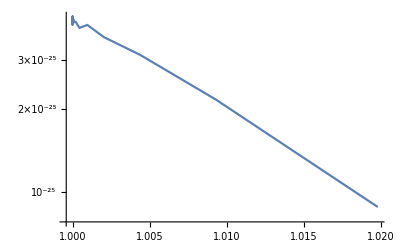

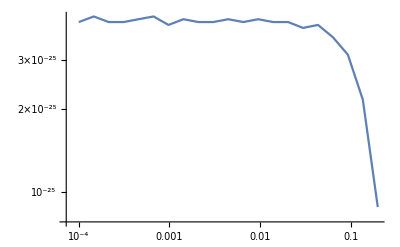

```mathematica
ListLogPlot[Transpose[{MD2v,svv}],Joined ->True,PlotRange->All]
ListLogLogPlot[Transpose[{delv,svv}],Joined ->True]
```

```mathematica
(*Here I take into account that sin alpha is epsilon dependent*)
del=.
ieps=2;
ivrel=1;
idel=4;
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],MD2->Sqrt[MD1^2+del^2],s->MD1 ^2(1+epsv),sa->-sw eps/cw};
svs=Simplify[Series[sv//.replcoann,{eps,0,ieps},{epsv,0,ivrel},{del,0,idel}], assum]
```

((1/(2 cw^4 epsv MZ^4 MZp^4)alph alphX ctheta^2 √(epsv^2) π stheta^2 (5 MZ^4+2 cw^2 MZ^4+cw^4 MZ^4-2 cw^2 MZ^2 MZp^2-2 cw^4 MZ^2 MZp^2+cw^4 MZp^4-10 MZ^4 sw^2-2 cw^2 MZ^4 sw^2+10 MZ^2 MZp^2 sw^2+4 cw^2 MZ^2 MZp^2 sw^2-2 cw^2 MZp^4 sw^2+5 MZ^4 sw^4-10 MZ^2 MZp^2 sw^4+5 MZp^4 sw^4) epsv+O[epsv]^2) del^2+(-1/(4 (cw^4 epsv MD1^2 MZ^4 MZp^4))alph alphX ctheta^2 √(epsv^2) π stheta^2 (5 MZ^4+2 cw^2 MZ^4+cw^4 MZ^4-2 cw^2 MZ^2 MZp^2-2 cw^4 MZ^2 MZp^2+cw^4 MZp^4-10 MZ^4 sw^2-2 cw^2 MZ^4 sw^2+10 MZ^2 MZp^2 sw^2+4 cw^2 MZ^2 MZp^2 sw^2-2 cw^2 MZp^4 sw^2+5 MZ^4 sw^4-10 MZ^2 MZp^2 sw^4+5 MZp^4 sw^4)+1/(4 cw^4 epsv MD1^2 MZ^4 MZp^4)alph alphX ctheta^2 √(epsv^2) π stheta^2 (5 MZ^4+2 cw^2 MZ^4+cw^4 MZ^4-2 cw^2 MZ^2 MZp^2-2 cw^4 MZ^2 MZp^2+cw^4 MZp^4-10 MZ^4 sw^2-2 cw^2 MZ^4 sw^2+10 MZ^2 MZp^2 sw^2+4 cw^2 MZ^2 MZp^2 sw^2-2 cw^2 MZp^4 sw^2+5 MZ^4 sw^4-10 MZ^2 MZp^2 sw^4+5 MZp^4 sw^4) epsv+O[epsv]^2) del^4+O[del]^5) eps^2+O[eps]^3

```mathematica
SeriesCoefficient[svs,{2}]/.reply/.MZp->0//Simplify
```

((alph ctheta^2 √(epsv^2) π stheta^2 (5+2 cw^2+cw^4-10 sw^2-2 cw^2 sw^2+5 sw^4) y epsv)/(2 cw^4 eps^2 epsv MD1^4)+O[epsv]^2) del^2+(-(alph ctheta^2 √(epsv^2) π stheta^2 (5+2 cw^2+cw^4-10 sw^2-2 cw^2 sw^2+5 sw^4) y)/(4 (cw^4 eps^2 epsv MD1^6))+(alph ctheta^2 √(epsv^2) π stheta^2 (5+2 cw^2+cw^4-10 sw^2-2 cw^2 sw^2+5 sw^4) y epsv)/(4 cw^4 eps^2 epsv MD1^6)+O[epsv]^2) del^4+O[del]^5

```mathematica
reply={alphX->y/eps^2*MZp^4/MD1^4};
is={2,2,1};
SeriesCoefficient[svs,is]*eps^is[[1]]*epsv^is[[3]]*del^is[[2]]/.reply/.MZp->0//.sw->Sqrt[1-cw^2]//Simplify
is={2,4,1};
SeriesCoefficient[svs,is]*eps^is[[1]]*epsv^is[[3]]*del^is[[2]]/.reply/.MZp->0//.sw->Sqrt[1-cw^2]//Simplify
is={2,4,0};
SeriesCoefficient[svs,is]*eps^is[[1]]*epsv^is[[3]]*del^is[[2]]/.reply/.MZp->0//.sw->Sqrt[1-cw^2]//Simplify
```

(4 alph ctheta^2 del^2 √(epsv^2) π stheta^2 y)/MD1^4

(2 alph ctheta^2 del^4 √(epsv^2) π stheta^2 y)/MD1^6

-(2 alph ctheta^2 del^4 √(epsv^2) π stheta^2 y)/(epsv MD1^6)

## Getting cross - section chi1 e-> chi2 e Zp (same as for full)

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e-vSam-Zp.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

ME

ME

MD2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power}/.ME->0//Simplify
```

(ca^2 ctheta^2 EE^2 eta^2 gX^2 stheta^2 (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2) (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/(4 chi^2 cw^2 sw^2 (-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(*(*relative velo in NR limit*)
sol=Solve[4p1cm/Sqrt[s]==vrel,s]/.ME->0
ss=Simplify[Series[s/.sol[[1,1]],{vrel,0,2}],assum];
s1=SeriesCoefficient[ss,0]+SeriesCoefficient[ss,2]vrel^2*)
```

```mathematica
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
```

```mathematica
sv=sig0*(IntMp-IntMm);
```

```mathematica
ptest=MD1/30/.params
ss=Solve[p1cm==ptest,s]/.params
tpt=tp/.ss[[2,1]]//.params
tmt=tm/.ss[[2,1]]//.params
If[tpt>tmt,sv/.ss[[2,1]]//.params,-sv/.ss[[2,1]]//.params]*GeVm2toPb
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.MD2->1.02
```

0.0333333

{{s→0.935511},{s→1.06893}}

0.973305

0.971467

6.75237×10^-26

6.8679×10^-26

```mathematica
chi->epsilon Power[cw,-1],eta->chi Power[1-Power[chi,2],-1/2]
```

```mathematica
(*Here I take into account that sin alpha is epsilon dependent*)
ieps=2;
ivrel=2;
isa=1;
idel=4;
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],MD2->Sqrt[MD1^2+del^2],s->MD1^2(1+epsv),sa->-sw eps/cw};
svs=Simplify[Series[sv//.replcoann,{eps,0,ieps},{epsv,0,ivrel},{del,0,idel}]/.sw->Sqrt[1-cw^2], assum]
```

((-(2 (alph alphX ctheta^2 √(epsv^2) π stheta^2) del^4)/(epsv MD1^2 MZp^4)+O[del]^5)+((4 alph alphX ctheta^2 √(epsv^2) π stheta^2 del^2)/(epsv MZp^4)+(2 alph alphX ctheta^2 √(epsv^2) π stheta^2 del^4)/(epsv MD1^2 MZp^4)+O[del]^5) epsv+(-(2 (alph alphX ctheta^2 √(epsv^2) MD1^2 π stheta^2))/(epsv MZp^4)-(4 (alph alphX ctheta^2 √(epsv^2) π stheta^2) del^2)/(epsv MZp^4)+(alph alphX ctheta^2 √(epsv^2) (16 MD1^2-17 MZp^2) π stheta^2 del^4)/(4 epsv MD1^2 MZp^6)+O[del]^5) epsv^2+O[epsv]^3) eps^2+O[eps]^3

```mathematica
reply={alphX->y/eps^2*MZp^4/MD1^4};
is={2,0,4};
SeriesCoefficient[svs,is]*eps^is[[1]]*vrel^is[[2]]*del^is[[3]]/.reply/.MZp->0
is={2,1,2};
SeriesCoefficient[svs,is]*eps^is[[1]]*vrel^is[[2]]*del^is[[3]]/.reply/.MZp->0
is={2,1,4};
SeriesCoefficient[svs,is]*eps^is[[1]]*vrel^is[[2]]*del^is[[3]]/.reply/.MZp->0
```

-(2 alph ctheta^2 del^4 √(epsv^2) π stheta^2 y)/(epsv MD1^6)

(4 alph ctheta^2 del^2 √(epsv^2) π stheta^2 vrel y)/(epsv MD1^4)

(2 alph ctheta^2 del^4 √(epsv^2) π stheta^2 vrel y)/(epsv MD1^6)

## Getting cross - section chi1 e-> chi2 e Zp (m2= m1+del)

### getting M^2

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e-vSam-Zp.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

ME

ME

MD2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power}/.ME->0//Simplify
```

(ca^2 ctheta^2 EE^2 eta^2 gX^2 stheta^2 (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2) (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/(4 chi^2 cw^2 sw^2 (-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* Amplitude squared in eps->0 limit, propto eps^2*)
Msq//.{ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
Series[%,{eps,0,2}]/.sw->Sqrt[1-cw^2];
Msqlim=SeriesCoefficient[%,2]*eps^2
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/((-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
Msqlimc1c2=Msqlim/.MD2->MD1//Simplify
Msqlimc1c1
Msqlimc1c2/Msqlimc1c1
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)

(2 EE^2 eps^2 gX^2 stheta^4 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)

ctheta^2/stheta^2

### getting xsections and testing limit MD2->MD1 analytics ok

```mathematica
(* cross-section*)
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
sv=sig0*(IntMp-IntMm);
```

```mathematica
(* cross-section eps->0 limit, propto eps^2*)
IntM=Integrate[Msqlim,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
svlim=sig0*(IntMp-IntMm);
```

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
svlimc1c2=svlim/.MD2->MD1//Simplify
svlimc1c1
Rsv=svlimc1c2/svlimc1c1
```

(ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s]))/(8 π (MD1^2-s)^2)

(EE^2 eps^2 gX^2 stheta^4 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s]))/(8 π (MD1^2-s)^2)

ctheta^2/stheta^2

```mathematica
(*Weird, when I first give all params except M2 and then M2 it gives a different numerical result...*)
ptest=MD1/30/.params;
ss=Solve[p1cm==ptest,s]/.params
tpt=tp/.ss[[2,1]]//.params;
tmt=tm/.ss[[2,1]]//.params;
If[tpt>tmt,sv/.ss[[2,1]]//.params,-sv/.ss[[2,1]]//.params]*GeVm2toPb
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.paramsnoMD2/.params
(*test0*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
test*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.vrel->4*ptest/MD1//.params*)
```

{{s→0.935511},{s→1.06893}}

6.75237×10^-26

6.8679×10^-26

6.54179×10^-26

6.8679×10^-26

```mathematica
myvrel=4*ptest/MD1//.params
mys=MD1^2(1+myvrel/2)//.params
```

0.133333

1.06667

```mathematica
svlimc1c1*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
svlimc1c1*Rsv*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
```

4.15061×10^-35

4.15061×10^-25

### getting series of xsection in del=MD2-MD1 limit for vrel small: series in del first and vrel after ok while series in vrel first del after negative

```mathematica
Series[svlim/.MD2->MD1+del,{del,0,0}]//Normal;
Series [%/.s->MD1^2(1+vrel/2),{vrel,0,2}]//Normal
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2)/(32 MZp^4 π)

4.1544×10^-25

```mathematica
Series [svlim/.s->MD1^2(1+vrel/2),{vrel,0,2}]//Normal;
Simplify[Series[%/.MD2->MD1+del,{del,0,0}]//Normal,assum]
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2)/(32 MZp^4 π)

-4.1544×10^-25

```mathematica
Series[svlim/.MD2->MD1+del/.s->MD1^2(1+vrel/2),{eps,0,2},{del,0,0},{vrel,0,2}]//Normal
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
Series[svlim/.MD2->MD1+del/.s->MD1^2(1+vrel/2),{del,0,0},{vrel,0,2}]//Normal
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
Series[svlim/.MD2->MD1+del/.s->MD1^2(1+vrel/2),{vrel,0,2},{del,0,0}]//Normal
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1}//.params
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2)/(32 MZp^4 π)

4.1544×10^-25

(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2)/(32 MZp^4 π)

4.1544×10^-25

-(ctheta^2 √(del^2) EE^2 eps^2 gX^2 MD1 stheta^2 vrel √(MD1^2 vrel^2))/(32 del MZp^4 π)

-4.1544×10^-25

### Testing different expansion orders: often negative numbers, seems that some NLO terms are very large

```mathematica
(*Here I test different expansions and check up to which order I have to go to get the right Xsection*)

(*non sense*)
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};

ieps=2;
ivrel=1;
idel=1;
Series[svlim/.MD2->MD1+del/.s->MD1^2(1+vrel/2),{eps,0,ieps},{del,0,idel},{vrel,0,ivrel}]//Normal;
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,epsv->vrel/2,vrel->4*ptest/MD1,alphX->aX}//.params

(*non sense*)
ieps=2;
ivrel=1;
idel=2;
Series[svlim/.MD2->MD1+del/.s->MD1^2(1+vrel/2),{eps,0,ieps},{del,0,idel},{vrel,0,ivrel}]//Normal;
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,epsv->vrel/2,vrel->4*ptest/MD1,alphX->aX}//.params

(*non sense*)
ieps=2;
ivrel=2;
idel=1;
Series[svlim/.MD2->MD1+del/.s->MD1^2(1+vrel/2),{eps,0,ieps},{del,0,idel},{vrel,0,ivrel}]//Normal;
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,epsv->vrel/2,vrel->4*ptest/MD1,alphX->aX}//.params

ieps=2;
ivrel=2;
idel=2;
Series[svlim/.MD2->MD1+del/.s->MD1^2(1+vrel/2),{eps,0,ieps},{del,0,idel},{vrel,0,ivrel}]//Normal;
%//.replcoann//.reply
%//Simplify
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,epsv->vrel/2,vrel->4*ptest/MD1,alphX->aX}//.params
```

-4.98529×10^-25

-3.63926×10^-25

-4.98529×10^-26

eps^2 ((alph ctheta^2 π stheta^2 vrel^2 y)/(2 eps^2 MD1^2)+del (-(4 alph ctheta^2 π stheta^2 vrel y)/(eps^2 MD1^3)+(2 alph ctheta^2 π stheta^2 vrel^2 y)/(eps^2 MD1^3))+del^2 ((8 alph ctheta^2 π stheta^2 y)/(eps^2 MD1^4)-(6 alph ctheta^2 π stheta^2 vrel y)/(eps^2 MD1^4)-(alph ctheta^2 (16 MD1^2-21 MZp^2) π stheta^2 vrel^2 y)/(4 eps^2 MD1^4 MZp^2)))

(alph ctheta^2 π stheta^2 (8 del MD1 MZp^2 (-2+vrel) vrel+2 MD1^2 MZp^2 vrel^2+del^2 (-16 MD1^2 vrel^2+MZp^2 (32-24 vrel+21 vrel^2))) y)/(4 MD1^4 MZp^2)

8.64914×10^-26

```mathematica
Series[svlim/.MD2->MD1+del,{del,0,0}]//Normal;
%*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.del->MD2-MD1//.params
Series[svlim/.MD2->MD1+del,{del,0,1}]//Normal;
%*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.del->MD2-MD1//.params
Series[svlim/.MD2->MD1+del,{del,0,2}]//Normal;
%*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.del->MD2-MD1//.params
Series[svlim/.MD2->MD1+del,{del,0,3}]//Normal;
%*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.del->MD2-MD1//.params
Series[svlim/.MD2->MD1+del,{del,0,4}]//Normal;
%*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.del->MD2-MD1//.params
Series[svlim/.MD2->MD1+del,{del,0,11}]//Normal;
%*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.del->MD2-MD1//.params
```

4.1783×10^-25

-6.54079×10^-26

7.033×10^-26

7.29376×10^-26

7.29736×10^-26

7.29741×10^-26

```mathematica
svlim*GeVm2toPb/.eps->epsilon/.s->MD1^2(1+vrel/2)/.vrel->4ptest/MD1//.params
Series[svlim/.s->MD1^2(1+vrel/2),{vrel,0,0}]//Normal;
%*GeVm2toPb/.eps->epsilon/.vrel->4ptest/MD1//.params
Series[svlim/.s->MD1^2(1+vrel/2),{vrel,0,1}]//Normal;
%*GeVm2toPb/.eps->epsilon/.vrel->4ptest/MD1//.params
Series[svlim/.s->MD1^2(1+vrel/2),{vrel,0,2}]//Normal;
%*GeVm2toPb/.eps->epsilon/.vrel->4ptest/MD1//.params
Series[svlim/.s->MD1^2(1+vrel/2),{vrel,0,5}]//Normal;
%*GeVm2toPb/.eps->epsilon/.vrel->4ptest/MD1//.params
```

5.86621×10^-26

-1.52595×10^-25

3.61331×10^-25

-8.91543×10^-26

-6.04766×10^-26

### Plots of Xsection dependence as a function of del= MD2-MD1

```mathematica
dmax=Log10[0.02]
dmin= -4
Nstep=20
step=(dmax-dmin)/Nstep
delv=Table[10^((dmin+(i-1)step)),{i,1,Nstep+1}]/.params
MD2v=MD1+delv/.params
svv=Table[If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.MD2->MD2v[[i]],{i,1,Nstep+1}]
```

-1.69897

-4

20

0.115051

{0.0001,0.000130332,0.000169865,0.000221388,0.00028854,0.00037606,0.000490127,0.000638794,0.000832553,0.00108508,0.00141421,0.00184317,0.00240225,0.0031309,0.00408057,0.0053183,0.00693145,0.0090339,0.0117741,0.0153454,0.02}

{1.0001,1.00013,1.00017,1.00022,1.00029,1.00038,1.00049,1.00064,1.00083,1.00109,1.00141,1.00184,1.0024,1.00313,1.00408,1.00532,1.00693,1.00903,1.01177,1.01535,1.02}

{4.14527×10^-25,4.12074×10^-25,4.07168×10^-25,4.09621×10^-25,4.09621×10^-25,4.04716×10^-25,4.04716×10^-25,4.04716×10^-25,3.97357×10^-25,3.87546×10^-25,3.80187×10^-25,3.72829×10^-25,3.60565×10^-25,3.43395×10^-25,3.26225×10^-25,3.01697×10^-25,2.72263×10^-25,2.28112×10^-25,1.7415×10^-25,1.25094×10^-25,6.8679×10^-26}

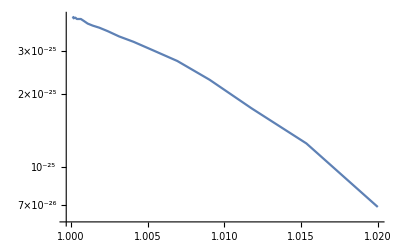

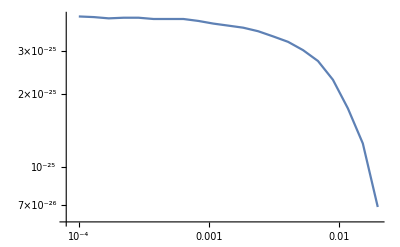

```mathematica
ListLogPlot[Transpose[{MD2v,svv}],Joined ->True,PlotRange->All]
ListLogLogPlot[Transpose[{delv,svv}],Joined ->True]
```

## Getting cross - section chi1 e-> chi2 e Zp (test=(m2-m1)/m1, vrel=test x nv) BEST OPTION

### getting M^2

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e-vSam-Zp.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&T>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME,T}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&T>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME|T)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

ME

ME

MD2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power}/.ME->0//Simplify
```

(ca^2 ctheta^2 EE^2 eta^2 gX^2 stheta^2 (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2) (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/(4 chi^2 cw^2 sw^2 (-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* Amplitude squared in eps->0 limit, propto eps^2*)
Msq//.{ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
Series[%,{eps,0,2}]/.sw->Sqrt[1-cw^2];
Msqlim=SeriesCoefficient[%,2]*eps^2
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/((-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
Msqlimc1c2=Msqlim/.MD2->MD1//Simplify
Msqlimc1c1
Msqlimc1c2/Msqlimc1c1
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)

Msqlimc1c1

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/(Msqlimc1c1 (-2 MD1^2+MZp^2+s+t)^2)

### getting xsections and testing limit MD2->MD1 analytics ok

```mathematica
(* cross-section*)
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
sv=sig0*(IntMp-IntMm);
```

```mathematica
(* cross-section eps->0 limit, propto eps^2*)
IntM=Integrate[Msqlim,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
svlim=sig0*(IntMp-IntMm);
```

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
svlimc1c2=svlim/.MD2->MD1//Simplify
svlimc1c1
Rsv=svlimc1c2/svlimc1c1
```

1/(8 π (MD1^2-s)^2)ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s])

svlimc1c1

1/(8 π (MD1^2-s)^2 svlimc1c1)ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s])

```mathematica
(*Weird, when I first give all params except M2 and then M2 it gives a different numerical result...*)
ptest=MD1/30/.params;
ss=Solve[p1cm==ptest,s]/.params
tpt=tp/.ss[[2,1]]//.params;
tmt=tm/.ss[[2,1]]//.params;
If[tpt>tmt,sv/.ss[[2,1]]//.params,-sv/.ss[[2,1]]//.params]*GeVm2toPb
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.paramsnoMD2/.params
(*test0*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
test*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.vrel->4*ptest/MD1//.params*)
```

{{s→0.935511},{s→1.06893}}

6.75237×10^-26

6.8679×10^-26

6.54179×10^-26

6.8679×10^-26

```mathematica
myvrel=4*ptest/MD1//.params
mys=MD1^2(1+myvrel/2)//.params
```

0.133333

1.06667

```mathematica
svlimc1c1*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
svlimc1c1*Rsv*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
```

3.89379×10^8 svlimc1c1

4.15061×10^-25

### getting series of xsection in test=(MD2-MD1)/MD1=test and vrel =2 (2+test) test+test2

```mathematica
Series[svlim//.{MD2->MD1(1+test),s->MD1^2(1+vrel/2),vrel->(4+2test)test+test2},{test,0,1},{test2,0,2}]//Normal;
svseries=Simplify[%,assum]
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1,test->del/MD1,test2->vrel-(4+2test)test}//.params
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (-1+2 test) test2^2)/(32 MZp^4 π)

6.19117×10^-26

```mathematica
Collect[svseries/.{test2-> vrel-(4+2test)test}/.vrel-> -(2 (MD1^2-s))/MD1^2/.test-> δ,s]
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 s stheta^2 (-1+2 δ) (-8/MD1^2-(4 δ (4+2 δ))/MD1^2))/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (-1+2 δ) (4+4 δ (4+2 δ)+δ^2 (4+2 δ)^2))/(32 MZp^4 π)

```mathematica
svseries//.replcoann//.reply
```

-(alph ctheta^2 π stheta^2 (-1+2 test) test2^2 y)/(2 MD1^2)

## Nastya’s edition

### Velocity and δ=(MD2-MD1)/MD1 expansion

#### Expanding in δ and test2=vrel-(4+2δ)δ

```mathematica
ClearAll[vrel];
```

```mathematica
σvSeries=Series[svlim//.{MD2->MD1(1+δ),s->MD1^2(1+vrel/2),vrel->(4+2δ)δ+test2},{δ,0,1},{test2,0,2}]//Normal//FullSimplify
```

$Aborted

```mathematica
σvSeriesGen=Series[sv//.{MD2->MD1(1+δ),s->MD1^2(1+vrel/2),vrel->(4+2δ)δ+test2},{δ,0,1},{test2,0,2}]//Normal//FullSimplify
```

-(ca^2 ctheta^2 EE^2 eta^2 gX^2 MD1^2 stheta^2 (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2) test2^2 (-1+2 δ))/(256 chi^2 cw^2 MZp^4 π sw^2)

```mathematica
(*σvSeries=
Collect[Simplify[σvSeries/.test2->vrel-(4+2δ)δ,assum],vrel]*)
```

```mathematica
σvSeries=-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2 (-1+2 δ))/(32 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ (2+δ) (-1+2 δ))/(8 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ^2 (2+δ)^2 (-1+2 δ))/(8 MZp^4 π);
```

```mathematica
(*σvSeries=Collect[Series[σvSeries,{δ,0,1}],vrel]*)
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ)/(4 MZp^4 π)+vrel^2 ((ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2)/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(16 MZp^4 π))

The structure of σvSeriesvrel is σvrel1 vrel + σvrel2 vrel^2

```mathematica
σvSeries/.δ-> 0.1//FullSimplify
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (-0.00795775+0.00795775 vrel) vrel)/MZp^4

Back to sBlock[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},

```mathematica
vrels=Solve[s==MD1^2(1+vrel/2),vrel][[1,1,2]]
```

-(2 (MD1^2-s))/MD1^2

```mathematica
σvSeries=Collect[Simplify[σvSeries/.vrel-> vrels,assum],s]
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
σvSeries/.δ-> 0.1//FullSimplify
```

(ctheta^2 EE^2 eps^2 gX^2 (0.0477465 MD1^4-0.0795775 MD1^2 s+0.031831 s^2) stheta^2)/(MD1^2 MZp^4)

The structure of σvSeries is σ0 + σ1 s + σ2 s^2

#### Expanding in δ and vrel (cross-check)

```mathematica
σvSeries2=Series[svlim//.{MD2->MD1(1+δ),s->MD1^2(1+vrel/2)},{δ,0,1},{vrel,4δ+2 δ^2,2}]//Normal;
```

```mathematica
σvSeries2=Collect[Series[σvSeries2,{δ,0,1}],vrel](*same as when expanded in δ and test2*)
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ)/(4 MZp^4 π)+vrel^2 ((ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2)/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(16 MZp^4 π))

```mathematica
σvSeries2/.δ->0.1//FullSimplify
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (-0.00795775+0.00795775 vrel) vrel)/MZp^4

## Averaged cross section numerically, mx=MD1

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ,nDM,nbFermions,nbBosons]
```

```mathematica
nDM[x_]:=4 π gDM MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nbFermions[x_]:=6 π gb Zeta[3] T^3/.T-> MD1/x;
nbBosons[x_]:=8 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

```mathematica
Plot3D[(mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ))/.{cosθ-> -1,mx-> 100},{Ex,100,10^6},{Eb,0,10^6},AxesLabel->{"Ex","Eb","smax"}]
```

-Graphics3D-

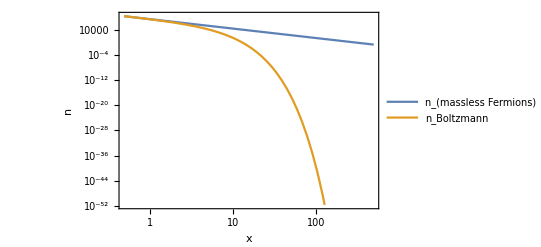

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nbFermions[x]/.gb-> 1],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nDM[x]/.gb-> 1]},{x,0,500},Frame->True,FrameLabel->{"x","n"},PlotLegends-> {"n_(massless Fermions)","n_Boltzmann"}]
```

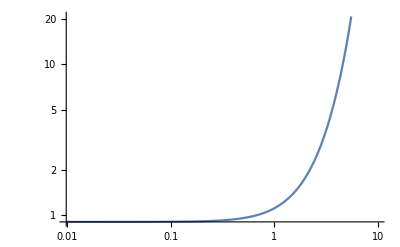

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nbFermions[x]/nDM[x]/.gb-> 1]},{x,0,10}]
```

#### Full integral

```mathematica
ss=sfromθ/.{Eb->  (Ep+Em)/2,Ex-> (Ep-Em)/2}
```

mx^2+(Em+Ep) (1/2 (-Em+Ep)-cosθ √(1/4 (-Em+Ep)^2-mx^2))

```mathematica
Solve[s==ss/.cosθ-> -1,Em]//FullSimplify
```

{{Em→-(Ep mx^2+√((Ep^2-s) (mx^2-s)^2))/s},{Em→(-Ep mx^2+√((Ep^2-s) (mx^2-s)^2))/s}}

```mathematica
Solve[s==ss/.cosθ-> 1,Em]//FullSimplify
```

{{Em→-(Ep mx^2+√((Ep^2-s) (mx^2-s)^2))/s},{Em→(-Ep mx^2+√((Ep^2-s) (mx^2-s)^2))/s}}

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
σvAveragedNR[x_]:=(x/m)/(8 m^4 BesselK[2,x]^2)NIntegrate[(σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1,{s,4 MD1^2,∞},WorkingPrecision->50]/.m-> MD1
```

```mathematica
σvAveragedFermionsN[x_]:=NIntegrate[(σvSeries(s-mx^2)1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T)HeavisideTheta[s-sfromθ/.cosθ-> 1]HeavisideTheta[-s+sfromθ/.cosθ->-1])/.mx-> MD1//.T-> MD1/x,{s,0,∞},{Eb,0,∞},{Ex,MD1,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->50]
```

```mathematica
listIntN=Transpose[{{1,10,50,100,500},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},σvAveragedFermionsN[#]&/@{1,10,50,100,500}]}]
```

NIntegrate::precw: The precision of the argument function ((ⅇ^(-Ex/100) (-10000+s) (5.75355×10^-8-9.51×10^-12 s+3.92975×10^-16 s^2) HeavisideTheta[10000+2 Eb (Ex+√(-10000+Power[«2»]))-s] HeavisideTheta[-10000-2 Eb (Ex-√Plus[«2»])+s])/(1+ⅇ^(Eb/100))) is less than WorkingPrecision (50.).

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::precw: The precision of the argument function ((ⅇ^(-Ex/10) (-10000+s) (5.75355×10^-8-9.51×10^-12 s+3.92975×10^-16 s^2) HeavisideTheta[10000+2 Eb (Ex+√(-10000+Power[«2»]))-s] HeavisideTheta[-10000-2 Eb (Ex-√Plus[«2»])+s])/(1+ⅇ^(Eb/10))) is less than WorkingPrecision (50.).

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::precw: The precision of the argument function ((ⅇ^(-Ex/2) (-10000+s) (5.75355×10^-8-9.51×10^-12 s+3.92975×10^-16 s^2) HeavisideTheta[10000+2 Eb (Ex+√(-10000+Power[«2»]))-s] HeavisideTheta[-10000-2 Eb (Ex-√Plus[«2»])+s])/(1+ⅇ^(Eb/2))) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{1,0},{10,0},{50,0},{100,0},{500,0}}

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedFermionsN[10],10]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
Integrand=σvSeries(s-mx^2)1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T)HeavisideTheta[s-sfromθ/.cosθ-> 1]HeavisideTheta[-s+sfromθ/.cosθ->-1];
```

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1,Ex=1000,Eb=10,s=20000},Integrand/.mx-> MD1//.T-> MD1/x]/.x-> 10//N
```

2.45374×10^-48

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1,Eb=10,s=20000},Integrand/.mx-> MD1//.T-> MD1/x]/.x-> 100//N
```

1.11341×10^-8 2.71828^(-1. Ex) HeavisideTheta[10000.-20. (Ex-1. √(-10000.+Ex^2))] HeavisideTheta[-10000.+20. (Ex+√(-10000.+Ex^2))]

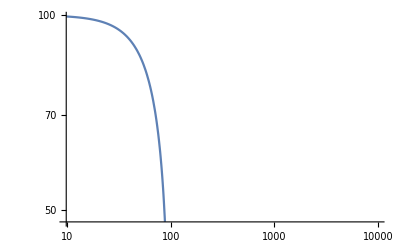

```mathematica
LogLogPlot[{Im[(Ex+√(-10000.+Ex^2))],Im[(Ex-1. √(-10000.+Ex^2))]},{Ex,0,10^4}]
```

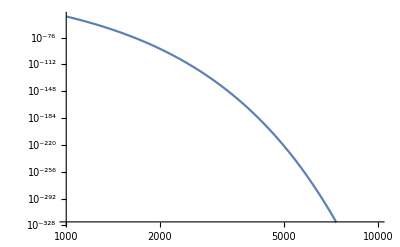

```mathematica
LogLogPlot[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1,Eb=10,s=20000},Integrand/.mx-> MD1//.T-> MD1/x]/.x-> 10//N,{Ex,1000,10^4}]
```

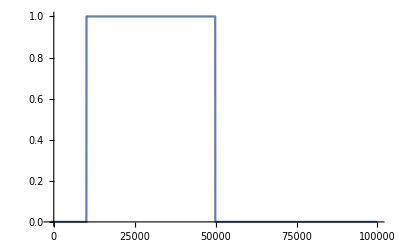

```mathematica
Plot[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,mx=100,δ=10^-2,Ex= 1000,T=10,Eb=10},HeavisideTheta[s-sfromθ/.cosθ-> 1]HeavisideTheta[-s+sfromθ/.cosθ->-1]],{s,-1000,10^5}]
```

#### Analytically over s, then numerically

```mathematica
sfromθ
```

mx^2+2 Eb (Ex-cosθ √(Ex^2-mx^2))

```mathematica
σvSeries=-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2 (-1+2 δ))/(32 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ (2+δ) (-1+2 δ))/(8 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ^2 (2+δ)^2 (-1+2 δ))/(8 MZp^4 π);
```

```mathematica
vrels=Solve[s==MD1^2(1+vrel/2),vrel][[1,1,2]]
```

-(2 (MD1^2-s))/MD1^2

```mathematica
σvSeries=Collect[Simplify[σvSeries/.vrel-> vrels,assum],s]
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
Sint=Integrate[σvSeries(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum]
```

-(ctheta^2 Eb^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (12 Eb^2 (2 Ex^3-Ex mx^2)+3 Ex (mx^2-MD1^2 (1+δ)^2)^2-4 Eb (4 Ex^2-mx^2) (-mx^2+MD1^2 (1+δ)^2)))/(3 MD1^2 MZp^4 π)

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},((2 π^2)/(nDM[x] nbFermions[x])Sint 1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1]
```

(49 ⅇ^(-(Ex x)/100) Eb^2 √(-10000+Ex^2) (121203 Ex-804 Eb (-10000+4 Ex^2)+12 Eb^2 (-10000 Ex+2 Ex^3)) x^4)/(145800000000000000000000000000 (1+ⅇ^((Eb x)/100)) π BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermionsSemiN[x_]:=(2 π^2)/(nDM[x] nbFermions[x])NIntegrate[(Sint 1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1,{Ex,MD1,∞},{Eb,0,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->20]
σvAveragedFermionsSemiNNReorderred[x_]:=(2 π^2)/(nDM[x] nbFermions[x])NIntegrate[(Sint 1/ⅇ^(Eb/T)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1,{Eb,0,∞},{Ex,MD1,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->20]

σvAveragedFermionsSemiNNR[x_]:=(2 π^2)/(nDM[x] nbFermions[x])NIntegrate[(Sint 1/ⅇ^(Eb/T)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1,{Ex,MD1,∞},{Eb,0,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->20]

σvAveragedNR[x_]:=(x/m)/(8 m^4 BesselK[2,x]^2)NIntegrate[(σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1,{s,4 MD1^2,∞},WorkingPrecision->20]/.m-> MD1
```

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiN[#]]&/@{1,20}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.000054931432057976757015,6.8329188095133730887×10^-9}

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiNNReorderred[#]]&/@{1,20}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.00005650335886682345518,6.9965502622927172224×10^-9}

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedNR[0.01]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.1145×10^10}. NIntegrate obtained 1.44864×10^25 and 3.08889×10^22 for the integral and error estimates.

4527.24

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiNNRmassive[0.01]]
```

NIntegrate::precw: The precision of the argument function (1.04793×10^-15 ⅇ^(-0.0001 Eb-0.0001 Ex) Eb^2 √(-10000+Ex^2) (1.323×10^7 Ex-8400. Eb (-10000+4 Ex^2)+12 Eb^2 (-10000 Ex+2 Ex^3))) is less than WorkingPrecision (20.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5021.55

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiNNR[0.01]]
```

NIntegrate::precw: The precision of the argument function (1.04793×10^-15 ⅇ^(-0.0001 Eb-0.0001 Ex) Eb^2 √(-10000+Ex^2) (1.323×10^7 Ex-8400. Eb (-10000+4 Ex^2)+12 Eb^2 (-10000 Ex+2 Ex^3))) is less than WorkingPrecision (20.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5021.55

```mathematica
listIntSemiN=Transpose[{{1,5,10,20,50,100,500},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiN[#]&/@{1,5,10,20,50,100,500}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1,0.000054931432057976757015},{5,2.7396933371509485649×10^-7},{10,4.404131011051305641×10^-8},{20,6.8329188095133730887×10^-9},{50,1.0603192542110393625×10^-9},{100,8.8246059634433136481×10^-10},{500,1.5321593835410300383×10^-9}}

```mathematica
listIntSemiNNR=Transpose[{{1,5,10,20,50,100,500},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiNNR[#]&/@{1,5,10,20,50,100,500}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1,0.00005650335886682345518},{5,2.7912867487207676271×10^-7},{10,4.4430799225606366807×10^-8},{20,6.9965502622927172224×10^-9},{50,1.2266273552035327948×10^-9},{100,1.018268607031666507×10^-9},{500,1.7099638027075202496×10^-9}}

```mathematica
listIntNR=Transpose[{{1,10,50,100,500},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedNR[#]&/@{1,10,50,100,500}]}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{1,0.0000600423},{10,3.51956×10^-7},{50,1.06423×10^-7},{100,7.20259×10^-8},{500,0.}}

NIntegrate::precw: The precision of the argument function ((-40000+s) √s (5.75355×10^-8-9.51×10^-12 s+3.92975×10^-16 s^2) BesselK[1,0.0100013 √s]) is less than WorkingPrecision (20.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {2.1875158059697448829×10^6}. NIntegrate obtained 1.2666504379114081953×10^7 and 0.23711357362091467677 for the integral and error estimates.

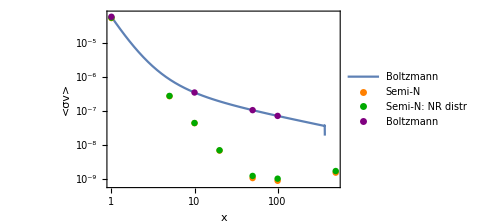

```mathematica
Show[{LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=10^-1},σvAveragedNR[x]]} ,{x,1,500},Frame->True,FrameLabel->{"x","<σv>"},PlotRange-> {{1,500},{7 10^-10,7 10^-5}},PlotLegends->{"Boltzmann"},ImageSize->Medium],ListLogLogPlot[listIntSemiN,PlotStyle->Orange,PlotLegends->{"Semi-N"}],ListLogLogPlot[listIntSemiNNR,PlotStyle->Darker[Green],PlotLegends->{"Semi-N: NR distr"}],ListLogLogPlot[listIntNR,PlotStyle->Purple,PlotLegends->{"Boltzmann"}]}]
```

## Analytical averaged cross section, no σ expansion, mx=MD1

#### Int over s, Eb & Ex

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

Integration over s

```mathematica
Sint=Collect[ Integrate[σvSeries(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum],{σ0,σ1,σ2}]
```

-1/(3 MD1^2 MZp^4 π)ctheta^2 Eb^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (12 Eb^2 (2 Ex^3-Ex mx^2)+3 Ex (mx^2-MD1^2 (1+δ)^2)^2-4 Eb (4 Ex^2-mx^2) (-mx^2+MD1^2 (1+δ)^2))

Integration over Eb - energy of a bath particle, separately for bosons and fermions (note that normalization number density is also different for these particles)

```mathematica
EbintFermions=Integrate[Sint/(ⅇ^(Eb/T)+1),{Eb,0,∞},Assumptions->assum]
```

-1/(3 MD1^2 MZp^4 π)ctheta^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (7/30 (4 Ex^2-mx^2) π^4 T^4 (mx^2-MD1^2 (1+δ)^2)+9/2 Ex T^3 (mx^2-MD1^2 (1+δ)^2)^2 Zeta[3]+270 (2 Ex^3-Ex mx^2) T^5 Zeta[5])

```mathematica
EbintBosons=Integrate[Sint/(ⅇ^(Eb/T)-1),{Eb,0,∞},Assumptions->assum]
```

Integration over Ex - energy of the DM particle (takes forever to calculate)

```mathematica
(*ExintFermions=Integrate[EbintFermions ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum]*)
```

```mathematica
ConditionalExpression[-1/(30 MD1^2 MZp^4 π)ctheta^2 EE^2 eps^2 gX^2 mx^2 stheta^2 T^4 (-1+2 δ) (mx T BesselK[1,mx/T] (7 mx^2 π^4-7 MD1^2 π^4 (1+δ)^2+16200 T^2 Zeta[5])+BesselK[2,mx/T] (28 mx^2 π^4 T^2+45 mx^4 Zeta[3]+45 MD1^4 (1+δ)^4 Zeta[3]-2 MD1^2 (1+δ)^2 (14 π^4 T^2+45 mx^2 Zeta[3])+2700 mx^2 T^2 Zeta[5]+64800 T^4 Zeta[5])), Re[T]>0]
```

```mathematica
ExintFermions=-1/(30 MD1^2 MZp^4 π)ctheta^2 EE^2 eps^2 gX^2 mx^2 stheta^2 T^4 (-1+2 δ) (mx T BesselK[1,mx/T] (7 mx^2 π^4-7 MD1^2 π^4 (1+δ)^2+16200 T^2 Zeta[5])+BesselK[2,mx/T] (28 mx^2 π^4 T^2+45 mx^4 Zeta[3]+45 MD1^4 (1+δ)^4 Zeta[3]-2 MD1^2 (1+δ)^2 (14 π^4 T^2+45 mx^2 Zeta[3])+2700 mx^2 T^2 Zeta[5]+64800 T^4 Zeta[5]));
```

```mathematica
(*ExintFermions=12 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+2/15 mx^2 T^4 σ1 (7 mx π^4 T BesselK[1,mx/T]+28 π^4 T^2 BesselK[2,mx/T]+90 mx^2 BesselK[2,mx/T] Zeta[3])+2/15 mx^2 T^4 σ2 (14 mx^3 π^4 T BesselK[1,mx/T]+56 mx^2 π^4 T^2 BesselK[2,mx/T]+90 mx^4 BesselK[2,mx/T] Zeta[3]+32400 mx T^3 BesselK[1,mx/T] Zeta[5]+5400 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5]);*)
```

```mathematica
(*ExintBosons=Collect[Integrate[EbintBosons ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σ0,σ1,σ2}]*)
```

```mathematica
(*ExintBosons=16 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+16/15 mx^2 T^4 σ1 (mx π^4 T BesselK[1,mx/T]+4 π^4 T^2 BesselK[2,mx/T]+15 mx^2 BesselK[2,mx/T] Zeta[3])+16/15 mx^2 T^4 σ2 (2 mx^3 π^4 T BesselK[1,mx/T]+8 mx^2 π^4 T^2 BesselK[2,mx/T]+15 mx^4 BesselK[2,mx/T] Zeta[3]+4320 mx T^3 BesselK[1,mx/T] Zeta[5]+720 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5]);*)
```

```mathematica
(ExintFermions-ExintBosons)//FullSimplify
```

#### Putting together <σv>

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ,nbFermions,nbBosons,nDM,IntFermions]
```

```mathematica
nDM[x_]:=4 π gDM MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nbFermions[x_]:=6 π gb Zeta[3] T^3/.T-> MD1/x;
nbBosons[x_]:=8 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
IntFermions[x_]:=ExintFermions/.mx-> MD1/.T-> MD1/x//FullSimplify
```

```mathematica
σvAveragedFermionsFunc[x_]:=(2 π^2)/(nDM[x] nbFermions[x])IntFermions[x]//FullSimplify
σvAveragedNR[x_]:=(x/m)/(8 m^4 BesselK[2,x]^2)NIntegrate[(σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1,{s,4 MD1^2,∞},WorkingPrecision->50]/.m-> MD1 (*non-relativistic medium frim Gondolo&Gelmini*)
```

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermionsFunc[30],10]]
```

7.20024×10^-10

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},σvAveragedFermionsFunc[30]]
```

7.20024×10^-10

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[500],10]]
```

4.919812404×10^-8

#### Plots

NIntegrate::precw: The precision of the argument function ((-40000+s) √s (14641/(81000000000 π)-(121 s)/(4050000000000 π)+s^2/(810000000000000 π)) BesselK[1,0.0100013 √s]) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {8.8924264840644084035725746841775090471607014084032×10^6}. NIntegrate obtained 1.2666504379114077495947049008504040625124276580291×10^7 and 8.6709790356016241052511436483219404002493512016217×10^-16 for the integral and error estimates.

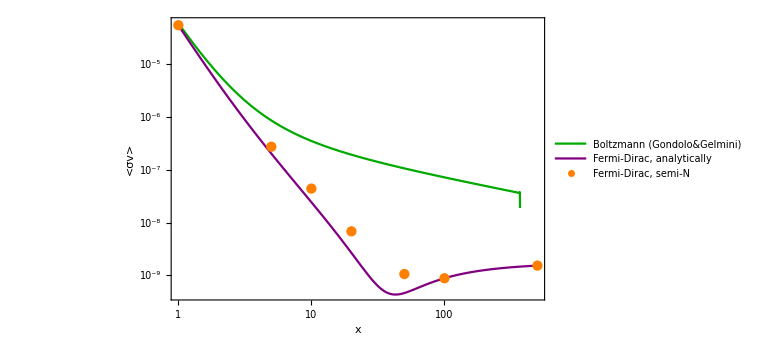

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[x],10]],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsFunc[x]]} ,{x,1,500},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},ImageSize->Large,PlotStyle->{Darker[Green],Purple},PlotLegends->{"Boltzmann (Gondolo&Gelmini)","Fermi-Dirac, analytically"}],ListLogLogPlot[listIntSemiN,PlotStyle->Orange,PlotLegends->{"Fermi-Dirac, semi-N"},PlotRange->{{1,500},Automatic}]]
```

Compare Semi-numerical and analytical results

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermionsFunc[#],10]&/@{1,5,10,20,50,100,500}]
```

{0.0000549165,2.03079×10^-7,2.43544×10^-8,2.66614×10^-9,4.63094×10^-10,8.82461×10^-10,1.53216×10^-9}

```mathematica
listIntSemiN
```

{{1,0.000054931432057976757015},{5,2.7396933371509485649×10^-7},{10,4.404131011051305641×10^-8},{20,6.8329188095133730887×10^-9},{50,1.0603192542110393625×10^-9},{100,8.8246059634433136481×10^-10},{500,1.5321593835410300383×10^-9}}

## Analytical averaged cross section, mx=MD1

#### Int over s, Eb & Ex

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

Integration over s

```mathematica
Sint=Collect[ Integrate[σvSeries(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum],{σ0,σ1,σ2}]
```

-(ctheta^2 Eb^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (12 Eb^2 (2 Ex^3-Ex mx^2)+3 Ex (mx^2-MD1^2 (1+δ)^2)^2-4 Eb (4 Ex^2-mx^2) (-mx^2+MD1^2 (1+δ)^2)))/(3 MD1^2 MZp^4 π)

Integration over Eb - energy of a bath particle, separately for bosons and fermions (note that normalization number density is also different for these particles)

```mathematica
EbintFermions=Collect[Integrate[Sint/(ⅇ^(Eb/T)+1),{Eb,0,∞},Assumptions->assum],{σ0,σ1,σ2}]
```

-(ctheta^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (7/30 (4 Ex^2-mx^2) π^4 T^4 (mx^2-MD1^2 (1+δ)^2)+9/2 Ex T^3 (mx^2-MD1^2 (1+δ)^2)^2 Zeta[3]+270 (2 Ex^3-Ex mx^2) T^5 Zeta[5]))/(3 MD1^2 MZp^4 π)

```mathematica
EbintBosons=Collect[Integrate[Sint/(ⅇ^(Eb/T)-1),{Eb,0,∞},Assumptions->assum],{σ0,σ1,σ2}]
```

-(ctheta^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (4/15 (4 Ex^2-mx^2) π^4 T^4 (mx^2-MD1^2 (1+δ)^2)+6 Ex T^3 (mx^2-MD1^2 (1+δ)^2)^2 Zeta[3]+288 (2 Ex^3-Ex mx^2) T^5 Zeta[5]))/(3 MD1^2 MZp^4 π)

Integration over Ex - energy of the DM particle (takes forever to calculate)

```mathematica
(*ExintFermions=Collect[Integrate[EbintFermions ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σ0,σ1,σ2}]*)
```

```mathematica
ExintFermions=12 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+2/15 mx^2 T^4 σ1 (7 mx π^4 T BesselK[1,mx/T]+28 π^4 T^2 BesselK[2,mx/T]+90 mx^2 BesselK[2,mx/T] Zeta[3])+2/15 mx^2 T^4 σ2 (14 mx^3 π^4 T BesselK[1,mx/T]+56 mx^2 π^4 T^2 BesselK[2,mx/T]+90 mx^4 BesselK[2,mx/T] Zeta[3]+32400 mx T^3 BesselK[1,mx/T] Zeta[5]+5400 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5]);
```

```mathematica
(*ExintBosons=Collect[Integrate[EbintBosons ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σ0,σ1,σ2}]*)
```

```mathematica
ExintBosons=16 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+16/15 mx^2 T^4 σ1 (mx π^4 T BesselK[1,mx/T]+4 π^4 T^2 BesselK[2,mx/T]+15 mx^2 BesselK[2,mx/T] Zeta[3])+16/15 mx^2 T^4 σ2 (2 mx^3 π^4 T BesselK[1,mx/T]+8 mx^2 π^4 T^2 BesselK[2,mx/T]+15 mx^4 BesselK[2,mx/T] Zeta[3]+4320 mx T^3 BesselK[1,mx/T] Zeta[5]+720 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5]);
```

```mathematica
(ExintFermions-ExintBosons)//FullSimplify
```

2/15 mx^2 T^4 (-mx T BesselK[1,mx/T] (π^4 (σ1+2 mx^2 σ2)+2160 T^2 σ2 Zeta[5])-2 BesselK[2,mx/T] (2 π^4 T^2 (σ1+2 mx^2 σ2)+15 (σ0+mx^2 σ1+mx^4 σ2) Zeta[3]+180 T^2 (mx^2+24 T^2) σ2 Zeta[5]))

#### Plugging in the cross section expansion coefficients

```mathematica
σSeriesIns={σ0-> (ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π),σ1-> (ctheta^2 EE^2 eps^2 gX^2 stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π),σ2-> (ctheta^2 EE^2 eps^2 gX^2  stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)};
```

```mathematica
IntBosons=ExintBosons/.mx-> MD1/.σSeriesIns/.T-> MD1/x//FullSimplify
```

(8 ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (-π^4 x^3 δ BesselK[3,x]-180 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

```mathematica
IntFermions=ExintFermions/.mx-> MD1/.σSeriesIns/.T-> MD1/x//FullSimplify
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (-7 π^4 x^3 δ BesselK[3,x]-1350 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

```mathematica
IntFermionsFunc[y_]:=IntFermions/.x-> y;
```

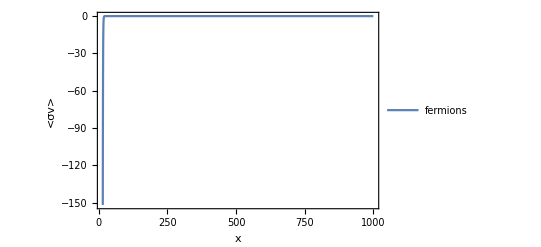

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},IntFermionsFunc[x]]} ,{x,15,1000},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

```mathematica
IntFermions
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (-7 π^4 x^3 δ BesselK[3,x]-1350 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

```mathematica
(IntBosons-IntFermions)//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (π^4 x^3 δ BesselK[3,x]+90 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

#### Putting together <σv>

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ]
```

```mathematica
nDM=4 π gDM MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nbFermions=6 π gb Zeta[3] T^3/.T-> MD1/x;
nbBosons=8 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
σvAveragedFermions=(2 π^2)/(nDM nbFermions)IntFermions//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (7 π^4 x^3 δ BesselK[3,x]+1350 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermions/.δ->1//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (7 π^4 x^3 BesselK[3,x]+1350 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedBosons=(2 π^2)/(nDM nbBosons)IntBosons//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (π^4 x^3 δ BesselK[3,x]+180 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(30 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
(σvAveragedFermions-σvAveragedBosons)//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (π^4 x^3 δ BesselK[3,x]+270 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermionsFunc[y_]:=σvAveragedFermions/.x-> y;
σvAveragedBosonsFunc[y_]:=σvAveragedBosons/.x-> y;
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermionsFunc[30],10]]
```

-0.875739

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermions,10]]
```

-(0.919459518 (-1119.88 (6. x BesselK[1.,x]+(24.+x^2) BesselK[2.,x])+68.1864 x^3 BesselK[3.,x]))/(x^4 BesselK[2.,x])

#### Non-relativistic medium

From Gondolo & Gelmini

```mathematica
ClearAll[σvAveragedNR]
```

```mathematica
(σ0+σ1 s+σ2 s^2)/.σSeriesIns
```

(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π)

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
σvAveragedNR[x_]:=NIntegrate[(2 π^2 m/x σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1,{s,4 MD1^2,∞}]
σvAveragedNRAnalytical[x_]:=Integrate[(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m])/.σSeriesIns/.m-> MD1,{s,4 MD1^2,∞}]
```

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNR[10]]
N[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNRAnalytical[10]] ,6]
```

4.41662×10^-6

ReplaceAll::reps: {σSeriesIns} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand 20 π^2 (-40000+s) √s (σ0+s σ1+s^2 σ2) BesselK[1,(√s)/10]/.σSeriesIns has evaluated to non-numerical values for all sampling points in the region with boundaries {{40001,41000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[20 π^2 (-40000+s) √s (σ0+s σ1+s^2 σ2) BesselK[1,(√s)/10]/.σSeriesIns,{s,40001,41000},WorkingPrecision→16.,AccuracyGoal→∞,PrecisionGoal→6.]

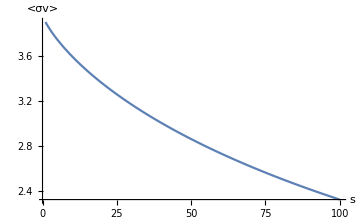

```mathematica
Plot[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},(-2 π^2 m/x σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1/.x-> 10] ,{s,1,100},AxesLabel->{"s","<σv>"},ImageSize->Medium,PlotRange->All]
```

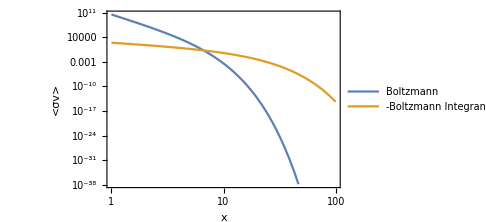

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedNR[x]],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},(-2 π^2 m/x σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1/.s-> 10^3]} ,{x,1,100},Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"Boltzmann","-Boltzmann Integrand"},ImageSize->Medium]
```

```mathematica
σvAveragedNRAnalytical[1.5]
```

ConditionalExpression[259433.-1. (1.+4. MD1^2)^1.5 (-8.52541×10^13 HypergeometricPFQRegularized[{1.5},{2.,2.5},0.00005625+0.000225 MD1^2]+8.52541×10^13 HypergeometricPFQRegularized[{1.5},{2.5,2.},0.00005625+0.000225 MD1^2]), ]

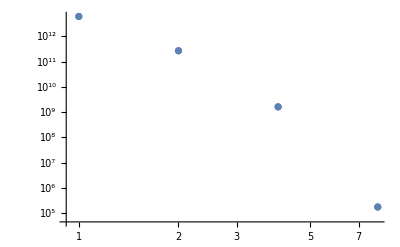

```mathematica
Show[ListLogLogPlot[Transpose[{PowerRange[1, 10,2],N[Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNRAnalytical[#]] ,6]&/@PowerRange[1, 10,2]}]],ListLogLogPlot[Transpose[{PowerRange[1, 10,2],N[Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNR[#]] ,6]&/@PowerRange[1, 10,2]}]]]
```

```mathematica
N[Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNRAnalytical[#]] ,6]/Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNR[#]]&/@PowerRange[1, 10,2]
```

{1.,1.,1.,1.}

#### Plots

```mathematica
(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m])/.σSeriesIns/.m-> MD1
```

1/x 2 MD1 π^2 √s (-4 MD1^2+s) ((ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π)) BesselK[1,(√s x)/MD1]

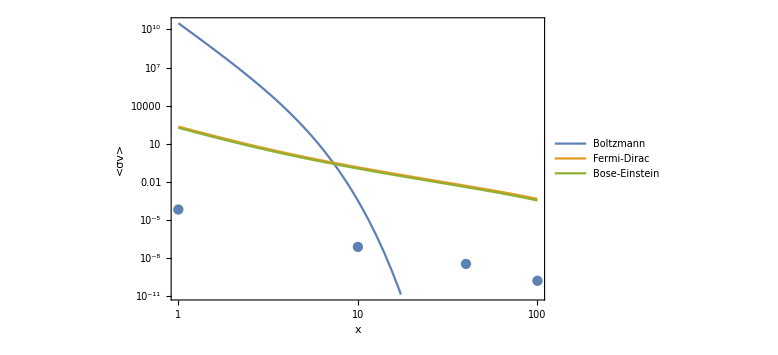

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedNR[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=150,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=150,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedBosonsFunc[x]]} ,{x,1,100},Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"Boltzmann","Fermi-Dirac","Bose-Einstein"},ImageSize->Large],ListLogLogPlot[listInt]]
```

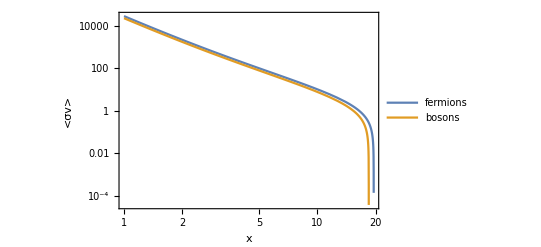

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

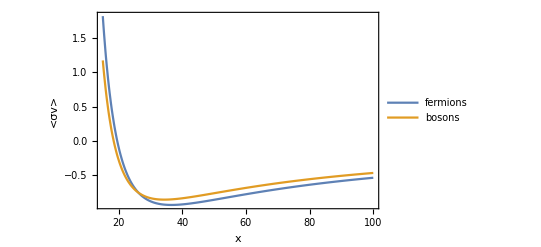

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,15,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

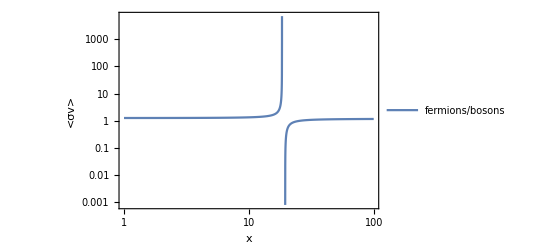

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]]/Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions/bosons"}]
```

```mathematica
Rasterize[LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.05},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.3},σvAveragedFermionsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"δ=0.05","δ=0.3"},ImageSize->Large]]
```

-Graphics-

```mathematica
ClearAll[plottingFunction]
```

```mathematica
δlist={0.01,0.5,1};
plottingFunction[x_]:=(Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5 ,MD1=100,δ=#},σvAveragedFermionsFunc[x]]&/@δlist);
Plot[plottingFunction[x],{x,0,1},PlotRange->All,PlotStyle->{"Red","Green","Blue"},PlotLegends->δlist,Frame->True,FrameLabel->{"x","<σv>"}]
```

-Graphics-

```mathematica
plottingFunction[x]
```

{-(0.91946 (-1119.88 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x])+68.1864 x^3 BesselK[3,x]))/(x^4 BesselK[2,x]),-(0.91946 (0.+340.932 x^3 BesselK[3,x]))/(x^4 BesselK[2,x]),-(0.91946 (7 π^4 x^3 BesselK[3,x]+1350 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(x^4 BesselK[2,x])}

## Averaged cross section by integration over vrel, mx=MD1

```mathematica
σvSeriesvrel
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ)/(4 MZp^4 π)+vrel^2 ((ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2)/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(16 MZp^4 π))

```mathematica
vrels=Solve[s==MD1^2(1+vrel/2),vrel][[1,1,2]]/.MD1-> mx
```

-(2 (mx^2-s))/mx^2

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

```mathematica
vrels/.s-> sfromθ/.cosθ-> 1
```

(4 Eb (Ex-√(Ex^2-mx^2)))/mx^2

```mathematica
vrels/.s-> sfromθ/.cosθ-> -1
```

(4 Eb (Ex+√(Ex^2-mx^2)))/mx^2

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},vrels/.s-> sfromθ/.cosθ-> -1]/.Ex-> 1000/.mx-> 100/.Eb-> 1000//N
```

797.995

Integration over s

```mathematica
vrelint=Collect[ Integrate[(σvrel1 vrel+σvrel2 vrel^2)(mx^2(1+vrel/2)-mx^2),{vrel,(vrels/.s-> sfromθ/.cosθ-> 1),(vrels/.s-> sfromθ/.cosθ->- 1)},Assumptions->assum],{σvrel1,σvrel2}]
```

((256 Eb^3 Ex^2 √(Ex^2-mx^2))/(3 mx^4)-(64 Eb^3 √(Ex^2-mx^2))/(3 mx^2)) σvrel1+((512 Eb^4 Ex^3 √((Ex-mx) (Ex+mx)))/mx^6-(256 Eb^4 Ex √((Ex-mx) (Ex+mx)))/mx^4) σvrel2

Integration over Eb - energy of a bath particle, separately for bosons and fermions (note that normalization number density is also different for these particles)

```mathematica
EbintFermions=Collect[Integrate[vrelint/(ⅇ^(Eb/T)+1),{Eb,0,∞},Assumptions->assum],{σvrel1,σvrel2}]
```

-(56 √(Ex^2-mx^2) (-4 Ex^2+mx^2) π^4 T^4 σvrel1)/(45 mx^4)-(5760 Ex √(Ex^2-mx^2) (-2 Ex^2+mx^2) T^5 σvrel2 Zeta[5])/mx^6

```mathematica
EbintBosons=Collect[Integrate[vrelint/(ⅇ^(Eb/T)-1),{Eb,0,∞},Assumptions->assum],{σvrel1,σvrel2}]
```

-(64 √(Ex^2-mx^2) (-4 Ex^2+mx^2) π^4 T^4 σvrel1)/(45 mx^4)-(6144 Ex √(Ex^2-mx^2) (-2 Ex^2+mx^2) T^5 σvrel2 Zeta[5])/mx^6

Integration over Ex - energy of the DM particle (takes forever to calculate)

```mathematica
Join[assum,Element[{σvrel1,σvrel2}, Reals]]
```

Join[{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&T>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME|T)∈ℝ},(σvrel1|σvrel2)∈ℝ]

```mathematica
(*ExintFermions=Collect[Integrate[EbintFermions ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->Join[assum,Element[{σvrel1,σvrel2}, Reals]]],{σvrel1,σvrel2}]*)
```

$Aborted

```mathematica
ExintFermions=(56 π^4 T^5 BesselK[3,mx/T])/(15 mx)σvrel1+(5760 T^6 σvrel2 BesselK[4,mx/T] Zeta[5])/mx^2;
```

```mathematica
(*ExintBosons=Collect[Integrate[EbintBosons ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σvrel1,σvrel2}]*)
```

#### Plugging in the cross section expansion coefficients

```mathematica
coef={σvrel1-> -(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(4 MZp^4 π),σvrel2-> ((ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2)/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(16 MZp^4 π))//FullSimplify};
```

```mathematica
IntBosons=ExintBosons/.mx-> MD1/.coef/.T-> MD1/x//FullSimplify;
```

```mathematica
IntFermions=ExintFermions/.mx-> MD1/.coef/.T-> MD1/x//FullSimplify
```

-(2 ctheta^2 EE^2 eps^2 gX^2 MD1^6 stheta^2 (7 π^4 x δ BesselK[3,x]+1350 (-1+2 δ) BesselK[4,x] Zeta[5]))/(15 MZp^4 π x^6)

```mathematica
IntFermionsFunc[y_]:=IntFermions/.x-> y;
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},IntFermionsFunc[10]]
```

-14.2311

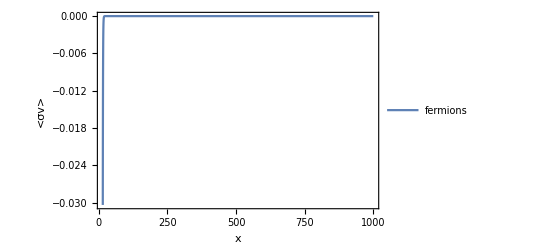

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},IntFermionsFunc[x]]} ,{x,15,1000},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

```mathematica
IntFermions
```

```mathematica
(IntBosons-IntFermions)//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (π^4 x^3 δ BesselK[3,x]+90 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

#### Putting together <σv>

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ]
```

```mathematica
nDM=4 π gDM MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nbFermions=6 π gb Zeta[3] T^3/.T-> MD1/x;
nbBosons=8 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
σvAveragedFermions=(2 π^2)/(nDM nbFermions)IntFermions//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (7 π^4 x^3 δ BesselK[3,x]+1350 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermions/.δ->1//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (7 π^4 x^3 BesselK[3,x]+1350 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedBosons=(2 π^2)/(nDM nbBosons)IntBosons//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (π^4 x^3 δ BesselK[3,x]+180 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(30 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
(σvAveragedFermions-σvAveragedBosons)//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (π^4 x^3 δ BesselK[3,x]+270 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermionsFunc[y_]:=σvAveragedFermions/.x-> y;
σvAveragedBosonsFunc[y_]:=σvAveragedBosons/.x-> y;
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=1},σvAveragedFermionsFunc[30]]
```

-24.4224

#### Non-relativistic medium

From Gondolo & Gelmini

```mathematica
ClearAll[σvAveragedNR]
```

```mathematica
σvAveragedNR[x_]:=NIntegrate[(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m]/.σSeriesIns/.m-> MD1),{s,4 MD1^2,∞}]
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedNR[100]]
```

1.2535×10^-77

#### Plots

```mathematica
(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m])/.σSeriesIns/.m-> MD1
```

1/x 2 MD1 π^2 √s (-4 MD1^2+s) ((ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π)) BesselK[1,(√s x)/MD1]

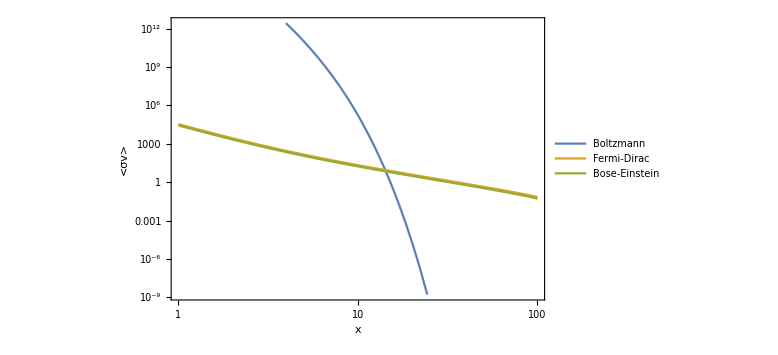

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedNR[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedBosonsFunc[x]]} ,{x,1,100},Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"Boltzmann","Fermi-Dirac","Bose-Einstein"},ImageSize->Large]]
```

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

-Graphics-

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,15,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

-Graphics-

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]]/Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions/bosons"}]
```

-Graphics-

```mathematica
Rasterize[LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.05},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.3},σvAveragedFermionsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"δ=0.05","δ=0.3"},ImageSize->Large]]
```

-Graphics-

```mathematica
ClearAll[plottingFunction]
```

```mathematica
δlist={0.01,0.5,1};
plottingFunction[x_]:=(Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5 ,MD1=100,δ=#},σvAveragedFermionsFunc[x]]&/@δlist);
Plot[plottingFunction[x],{x,0,1},PlotRange->All,PlotStyle->{"Red","Green","Blue"},PlotLegends->δlist,Frame->True,FrameLabel->{"x","<σv>"}]
```

-Graphics-

```mathematica
plottingFunction[x]
```

{-(0.91946 (-1119.88 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x])+68.1864 x^3 BesselK[3,x]))/(x^4 BesselK[2,x]),-(0.91946 (0.+340.932 x^3 BesselK[3,x]))/(x^4 BesselK[2,x]),-(0.91946 (7 π^4 x^3 BesselK[3,x]+1350 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(x^4 BesselK[2,x])}